# Angular momentum transfer from swift electrons to small polyhedral nanoparticles

## Definition of constants in a.u.

#### LAST EDITED

```mathematica
Now
```

Sun 3 Apr 2022 12:54:55GMT-5

#### Necessary packages to make graphs look better

```mathematica
Needs["MaTeX`"]
color={Orange,Blue,Red,Gray,Black,Magenta,Brown,Purple,Darker[Yellow]};
labels={"Sphere", "Icosahedron", "Dodecahedron", "Octahedron", "Hexahedron", "Tetrahedron"};
marker[col_,n_]:=Graphics[{col,Polygon[{Cos[2 Pi #/n],Sin[2 Pi #/n]}&/@Range[n]]},ImageSize->10]
```

#### Definition of constants

```mathematica
SetDirectory["/media/george/Almacenamiento/Ubuntu Storage/5-Maestria/0-Tesis/Sólidos platónicos/figs"];
hbar=6.582119569*10^(-16); (* eV s *) 
attosec=10^(-18);
atomicunitofspeed = 2.1877 ;(* x 10^8 cm/s*) (*value from Atomic units table.jpg*)
atomicunitoftime=24.189;(*as*)
fermivelocityofaluminum=2.03; (* x 10^8 cm/s*) (*value from Ashcroft page 38*)
alvf=fermivelocityofaluminum/atomicunitofspeed ;(*Al Fermi velocity in atomic units*)
nanometer=100/5.29177210903; (*nanometer in atomic units *)
electronVolt=0.0367493;
cSpeedLight=137.036;
qElectronCharge=-1;
electronCharge=-1;
(*Drude Aluminium*)
ωplasma= 13.142*electronVolt;(*Al*)                                                  
Γdamping=0.197*electronVolt;(*Al*)

(*Daniel Silver*)
(*ωplasma= 9.055*electronVolt;(*Ag*)                                                  
Γdamping=0.5*electronVolt;(*Ag*)*)

ΓsizeAla1nm = alvf/nanometer (*damping size correction for an a=1nm Al sphere Γc=A*(vF/R) with A=1 and R Np radius*)(* Kreibig book optical properties of metals pag 81*);
atomicunitofdistance=5.2918*10^-11;
SIunitofpolarizability=4π*(atomicunitofdistance)^3/(atomicunitoftime*attosec)*10^11;(*4π comes from the fact αSI = 4π αcgs*)
SIunitofforce=8.2387234983*10^-8;(*N*)
SIunitofmomentum=1.9928519128789674*10^-24;
```

#### Functions required

```mathematica
ϵDrudeAl[ωFreq_]=(1-ωplasma^2/(ωFreq(ωFreq + I (Γdamping))));
γLorentz[vel_]=1/(√(1-(vel/cSpeedLight)^2));
kWaveNumber[ωFreq_]=ωFreq/cSpeedLight;

Lorentzian[ω_,ω0_,Γ_,A_]:=(A*electronVolt^2)/(-ω^2+(ω0*electronVolt)^2-I ω (Γ*electronVolt)) (*In atomic units*)

ϵWernerAu[ω_]:=1+
Lorentzian[ω,0,.2,113.1]+
Lorentzian[ω,4,1.5,44.6]+
Lorentzian[ω,7.3,3.3,54.8]+
Lorentzian[ω,12.8,11.8,184.9]+(*Werner adjust using causal Lorentzians to REELS data[experimetal data until 70eV]*)
Lorentzian[ω,18.9,71,728.1]+
Lorentzian[ω,19.9,2.9,65.7]+
Lorentzian[ω,28.9,3.9,50]+
Lorentzian[ω,38.7,13,74.7]+
Lorentzian[ω,64.3,51.9,544]
```

## Introduction

The following notebook aims to compute the angular momentum transfer form swift electrons to small (1-5 nm of characteristic length) polyhedral nanoparticles. The polyhedra, also known as platonic solids, can be synthesized in a laboratory, in contrast with its spherical counterpart. Furthermore, the polyhedra symmetries allow the electrical response to be lineal. It follows from the above that the polarizability of polyhedra is proportional to the identity tensor→α_ij=α δ_ij, and thus it can be represented by one (scalar) component. Polyhedra are optically equivalent to spheres.

A method to compute angular momentum transfer from electrons to small particles has been reported [CASTELLANOS2021]. This method only requires the scalar polarizability of the nanoparticle. Also, expressions for the numerically calculated polarizability of polyhedra have been reported [SIHVOLA2004]. With the latter two results, angular momentum transfer from electrons to small polyhedra can be obtained and compared to the angular momentum transfer to small nanospheres, which has already been reported.

## Bohren Polarizabilities

Explain here...

#### Assigning every ellipsoid a number for easier recognition.

```mathematica
sphere=1;
prolate=2;
oblate=3;
labelsEllipsoid=MaTeX[{"\\text{sphere}","\\text{prolate}", "\\text{oblate}"}, FontSize->20];
```

#### Defining the polarizability of different polyhedra in terms of ε_i(ω)=ε(ω) and the volume V, where the inclusion are supposed to be embeded in vacuum with ε_e(ω)=1.

```mathematica
αPolEllipsoids[ωFreq_,ϵDielecFunc_,volume_, ellipsoidType_, eccentricity_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, ellipsoid=ellipsoidType, e=eccentricity, L1, L2, L3},
Switch[ellipsoid,(*Compare the variable ellipsoid to one of the possible solids*)
sphere,3/(4π)*V*(ϵ[ω]-1)/(ϵ[ω]+2){1,1,1},
prolate, L1=(1-e^2)/e^2(-1+1/(2e)Log[(1+e)/(1-e)]);L2=1/2(1-L1); L3=L2;3/(4π)*V*{(ϵ[ω]-1)/(3+3L1(ϵ[ω]-1)),(ϵ[ω]-1)/(3+3L2(ϵ[ω]-1)),(ϵ[ω]-1)/(3+3L3(ϵ[ω]-1))},
oblate, L1=1/(2 e^2)√((1-e^2)/e^2)(π/2-ArcTan[√((1-e^2)/e^2)])-(1-e^2)/(2 e^2);L2=L1; L3=(1-2L1);3/(4π)*V*{(ϵ[ω]-1)/(3+3L1(ϵ[ω]-1)),(ϵ[ω]-1)/(3+3L2(ϵ[ω]-1)),(ϵ[ω]-1)/(3+3L3(ϵ[ω]-1))}
]
]
```

```mathematica
αPolTheta[ωFreq_,ϵDielecFunc_,volume_, angleTheta_, eccentricity_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, ellipsoid=prolate, e=eccentricity, L1, L2, L3, θ=angleTheta,αDiag, RotMat},
L1=(1-e^2)/e^2(-1+1/(2e)Log[(1+e)/(1-e)]);
L2=1/2(1-L1); L3=L2;
αDiag=DiagonalMatrix[3/(4π)*V*{(ϵ[ω]-1)/(3+3L1(ϵ[ω]-1)),(ϵ[ω]-1)/(3+3L2(ϵ[ω]-1)),(ϵ[ω]-1)/(3+3L3(ϵ[ω]-1))}];
RotMat={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
RotMat.αDiag.Transpose[RotMat]
]
```

```mathematica
αPolThetaTest[ωFreq_,ϵDielecFunc_,volume_, angleTheta_, eccentricity_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, ellipsoid=sphere, e=eccentricity, θ=angleTheta,αDiag, RotMat},
αDiag=DiagonalMatrix[3/(4π)*V*(ϵ[ω]-1)/(ϵ[ω]+2){1,1,1}];
RotMat={{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}};
RotMat.αDiag.Transpose[RotMat]
]
```

#### Calculating α(t), in time space, via the Fast Fourier Transform

```mathematica
αdataEllipsoids[points_, range_, ϵDielecFunc_,αPolarizability_,volume_, ellipsoidType_, eccentricity_, direction_]:=Module[
{δω=range/points,δt=(2π)/range,ϵ=ϵDielecFunc,αα=αPolarizability,V=volume,  ellipsoid=ellipsoidType, e=eccentricity, i=direction,timeData,freqData, αωdata, αtdata},
timeData=Table[(j-(points/2))*δt,{j,1,points}]+$MachineEpsilon;
freqData=Table[(j-(points/2))*δω,{j,1,points}]+$MachineEpsilon;
αωdata=RotateLeft[Table[αα[freqData[[j]],ϵ,V, ellipsoid, e][[i]],{j,1,points}],points/2-1];
αtdata=Chop[RotateRight[InverseFourier[αωdata, FourierParameters->{-1, 1}],points/2-1]];
Table[{timeData[[j]],αtdata[[j]]*δω/(2π)},{j,1,points}]
]
```

```mathematica
ωs=ωplasma/√3;
Ωs=ωs √(1-(Γdamping/(2ωs))^2);
αα[t_,V_]=3/(4π)*V*HeavisideTheta[t] ωs^2/Ωs Exp[-t*Γdamping/2]Sin[Ωs*t];
```

```mathematica
num=2^17;
range=100; (*freq in eV*)
ee=0.5;
ellipsoid=prolate;
α1=Interpolation[Re[αdataEllipsoids[num, range, ϵDrudeAl, αPolEllipsoids, 4/3 π(1*nanometer)^3,ellipsoid, ee, 1]]];
alft1=ParallelTable[{t*atomicunitoftime,α1[t]*SIunitofpolarizability},{t,-50,200,0.1}];
α2=Interpolation[Re[αdataEllipsoids[num, range, ϵDrudeAl, αPolEllipsoids, 4/3 π(1*nanometer)^3,ellipsoid, ee, 2]]];
alft2=ParallelTable[{t*atomicunitoftime,α2[t]*SIunitofpolarizability},{t,-50,200,0.1}];
α3=Interpolation[Re[αdataEllipsoids[num, range, ϵDrudeAl, αPolEllipsoids, 4/3 π(1*nanometer)^3,ellipsoid, ee, 3]]];
alft3=ParallelTable[{t*atomicunitoftime,α3[t]*SIunitofpolarizability},{t,-50,200,0.1}];
```

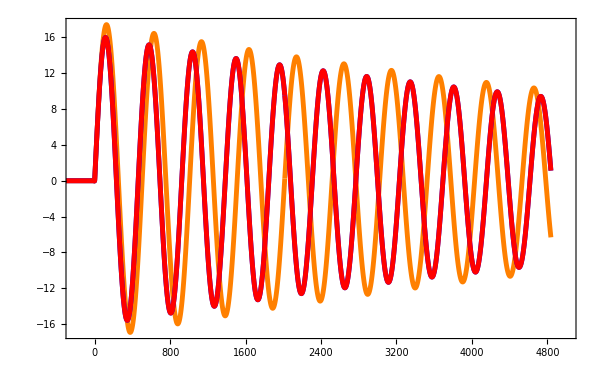

```mathematica
ListLinePlot[
{alft1,alft2,alft3},
InterpolationOrder->3,
PlotRange->{{-200,5000},Automatic},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\alpha_1","\\alpha_2","\\alpha_3","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Axis}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.93,0.22}],
ImageSize->600]
```

#### Poles of α for the ellipsoids

```mathematica
resonancesωEllipsoids[ϵDielecFunc_,ellipsoidType_, eccentricity_]:=Module[{ϵ=ϵDielecFunc,ellipsoid=ellipsoidType, L1, L2, L3, e=eccentricity},
(*Calculating the poles of the polarizability α*)
Switch[ellipsoid,
sphere,DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]+2==0,ω],x_/;x<1]//Sort,
prolate,L1=(1-e^2)/e^2(-1+1/(2e)Log[(1+e)/(1-e)]);L2=1/2(1-L1); L3=L2;DeleteCases[Re[ω/electronVolt]/.Join[NSolve[ϵ[ω]==1-1/L1,ω],NSolve[ϵ[ω]==1-1/L2,ω],NSolve[ϵ[ω]==1-1/L3,ω]],x_/;x<1]//Sort,
oblate, L1=1/(2 e^2)√((1-e^2)/e^2)(π/2-ArcTan[√((1-e^2)/e^2)])-(1-e^2)/(2 e^2);L2=L1; L3=(1-2L1);DeleteCases[Re[ω/electronVolt]/.Join[NSolve[ϵ[ω]==1-1/L1,ω],NSolve[ϵ[ω]==1-1/L2,ω],NSolve[ϵ[ω]==1-1/L3,ω]],x_/;x<1]//Sort
]]
resonancesEllipsoids[ellipsoidType_, eccentricity_]:=Module[{polyhedron=ellipsoidType, L1, L2, L3, e=eccentricity},
(*Calculating the poles of the polarizability α*)
Switch[polyhedron,
sphere,ϵ/.NSolve[ϵ+2==0,ϵ]//Sort,
prolate,L1=(1-e^2)/e^2(-1+1/(2e)Log[(1+e)/(1-e)]);L2=1/2(1-L1); L3=L2;ϵ/.{{ϵ->1-1/L1}, {ϵ->1-1/L2},{ϵ->1-1/L3}}//Sort,
oblate,L1=1/(2 e^2)√((1-e^2)/e^2)(π/2-ArcTan[√((1-e^2)/e^2)])-(1-e^2)/(2 e^2);L2=L1; L3=(1-2L1);ϵ/.{{ϵ->1-1/L1}, {ϵ->1-1/L2},{ϵ->1-1/L3}}//Sort
]]
```

```mathematica
DiagonalMatrix[{1,2,3}]
```

{{1,0,0},{0,2,0},{0,0,3}}

## Ari Sihvola Polarizabilities

Numerically calculated polarizabilities of polyhedra [SIHVOLA2004] are expressed in terms of dielectric function of the inclusions (particles) and dielectric function of the homogeneous medium, ε_i(ω) y ε_e(ω) respectively. The ratio of the dielectric functions is denoted by τ(ω)=ε_i(ω)/ε_e(ω). 

Polarizabilities α(ω) are presented in terms of Padé approximations, a quotient of polynomials. When numerical computations are being made, a Padé approximations is preferred over a truncate Taylor series because of the slower converge form the latter. However, when the polarizability is expressed in the form α(τ)→(τ-1)(P(τ))/(Q(τ)), the poles where  Q(τ)=0 can introduce unphysical resonances. For this reason, Fourier transforms of polarizabilities are computed in terms of Padé approximations and in terms of truncate Taylor series, and the results are then compared.

#### Assigning every polyhedra a number for easier recognition.

```mathematica
sphere=1;
icosahedron=2;
dodecahedron=3;
octahedron=4;
hexahedron=5;
tetrahedron=6;
labels=MaTeX[{"\\text{sphere}","\\text{icosahedron}", "\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}", "\\text{tetrahedron}"}, FontSize->20];
markers={Sphere[],Icosahedron[],Dodecahedron[],Octahedron[],Hexahedron[],Tetrahedron[]};
```

#### Defining the polarizability of different polyhedra in terms of ε_i(ω)=ε(ω) and the volume V, where the inclusion are supposed to be embeded in vacuum with ε_e(ω)=1.

```mathematica
αPol[ωFreq_,ϵDielecFunc_,volume_, polyhedronType_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, polyhedron=polyhedronType},
Switch[polyhedron,(*Compare the variable polyhedron to one of the possible platonic solids*)
sphere,3/(4π)*V*(ϵ[ω]-1)/(ϵ[ω]+2),
icosahedron,(3.1304)*V/(4π)*(ϵ[ω]-1)*(ϵ[ω]^2+3.04968ϵ[ω]+4.0896*1.5236/3.1304)/(ϵ[ω]^3+5.29169 ϵ[ω]^2+8.52687ϵ[ω]+4.0896),
dodecahedron, (3.1779)*V/(4π)*(ϵ[ω]-1)*(ϵ[ω]^2+2.42101ϵ[ω]+2.56842*1.5422/3.1779)/(ϵ[ω]^3+4.72932 ϵ[ω]^2+6.53464ϵ[ω]+2.56842),
octahedron,(3.5507)*V/(4π)*(ϵ[ω]-1)*(ϵ[ω]^3+5.13936 ϵ[ω]^2+5.86506ϵ[ω]+1.5871)/(ϵ[ω]^4+8.26227 ϵ[ω]^3+19.8267 ϵ[ω]^2+15.6191ϵ[ω]+3.5507),
hexahedron,(3.6442)*V/(4π)*(ϵ[ω]-1)*(ϵ[ω]^3+4.83981 ϵ[ω]^2+5.54742ϵ[ω]+1.6383)/(ϵ[ω]^4+8.0341 ϵ[ω]^3+19.3534 ϵ[ω]^2+15.4349ϵ[ω]+3.6442),
tetrahedron,(5.0285)*V/(4π)*(ϵ[ω]-1)*(ϵ[ω]^3+7.65667 ϵ[ω]^2+8.50919ϵ[ω]+1.8063)/(ϵ[ω]^4+14.1983 ϵ[ω]^3+44.9182 ϵ[ω]^2+30.2668ϵ[ω]+5.0285)
]
]
```

```mathematica
αPolTaylor[ωFreq_,ϵDielecFunc_,volume_, polyhedronType_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, polyhedron=polyhedronType},
Switch[polyhedron,(*Compare the variable polyhedron to one of the possible platonic solids*)
sphere,3/(4π)*V*(ϵ[ω]-1)/(ϵ[ω]+2),
icosahedron,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+0.15406*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.0461227*((ϵ[ω]-1)/(ϵ[ω]+2))^4+0.034121*((ϵ[ω]-1)/(ϵ[ω]+2))^5-0.018884*((ϵ[ω]-1)/(ϵ[ω]+2))^6),
dodecahedron, V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+0.23947*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.11731*((ϵ[ω]-1)/(ϵ[ω]+2))^4+0.097089*((ϵ[ω]-1)/(ϵ[ω]+2))^5-0.074184*((ϵ[ω]-1)/(ϵ[ω]+2))^6),
octahedron,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+0.52836*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.15702*((ϵ[ω]-1)/(ϵ[ω]+2))^4+0.22333*((ϵ[ω]-1)/(ϵ[ω]+2))^5-0.13073*((ϵ[ω]-1)/(ϵ[ω]+2))^6+0.14303*((ϵ[ω]-1)/(ϵ[ω]+2))^7-0.12520*((ϵ[ω]-1)/(ϵ[ω]+2))^8),
hexahedron,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+0.71355*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.34804*((ϵ[ω]-1)/(ϵ[ω]+2))^4+0.45065*((ϵ[ω]-1)/(ϵ[ω]+2))^5-0.39060*((ϵ[ω]-1)/(ϵ[ω]+2))^6+0.42727*((ϵ[ω]-1)/(ϵ[ω]+2))^7-0.44059*((ϵ[ω]-1)/(ϵ[ω]+2))^8),
tetrahedron,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.64265*((ϵ[ω]-1)/(ϵ[ω]+2))^4+1.25207*((ϵ[ω]-1)/(ϵ[ω]+2))^5-1.03851*((ϵ[ω]-1)/(ϵ[ω]+2))^6+1.52913*((ϵ[ω]-1)/(ϵ[ω]+2))^7-1.69626*((ϵ[ω]-1)/(ϵ[ω]+2))^8)
]
]
```

```mathematica
αPolTetra[ωFreq_,ϵDielecFunc_,volume_, degree_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, deg=degree},
Switch[deg,(*Compare the variable polyhedron to one of the possible platonic solids*)
1,3/(4π)*V*(ϵ[ω]-1)/(ϵ[ω]+2),
2,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3),
3, V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.64265*((ϵ[ω]-1)/(ϵ[ω]+2))^4),
4,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.64265*((ϵ[ω]-1)/(ϵ[ω]+2))^4+1.25207*((ϵ[ω]-1)/(ϵ[ω]+2))^5),
5,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.64265*((ϵ[ω]-1)/(ϵ[ω]+2))^4+1.25207*((ϵ[ω]-1)/(ϵ[ω]+2))^5-1.03851*((ϵ[ω]-1)/(ϵ[ω]+2))^6),
6,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.64265*((ϵ[ω]-1)/(ϵ[ω]+2))^4+1.25207*((ϵ[ω]-1)/(ϵ[ω]+2))^5-1.03851*((ϵ[ω]-1)/(ϵ[ω]+2))^6+1.52913*((ϵ[ω]-1)/(ϵ[ω]+2))^7),
7,V/(4π)(3*(ϵ[ω]-1)/(ϵ[ω]+2)+1.42812*((ϵ[ω]-1)/(ϵ[ω]+2))^3-0.64265*((ϵ[ω]-1)/(ϵ[ω]+2))^4+1.25207*((ϵ[ω]-1)/(ϵ[ω]+2))^5-1.03851*((ϵ[ω]-1)/(ϵ[ω]+2))^6+1.52913*((ϵ[ω]-1)/(ϵ[ω]+2))^7-1.69626*((ϵ[ω]-1)/(ϵ[ω]+2))^8)
]
]
```

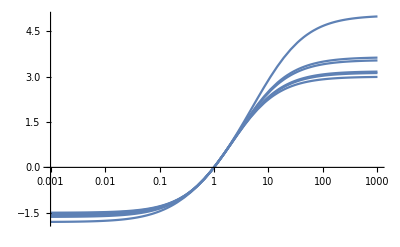

```mathematica
τ[ω]=ττ;
plots={};
For[i=1, i≤6,i++,
AppendTo[plots,LogLinearPlot[4π*αPol[ω,τ, 1,i],{ττ,10^-3,1000}, PlotRange->{{10^-3,10^3}, {-Automatic}}]]//Quiet
]
Show[plots, PlotRange->All]
```

#### Calculating α(t), in time space, via the Fast Fourier Transform

FFT explain

```mathematica
αdata[points_, range_, ϵDielecFunc_,αPolarizability_,volume_, polyhedronType_]:=Module[
{δω=range/points,δt=(2π)/range,ϵ=ϵDielecFunc,αα=αPolarizability,V=volume, polyhedron=polyhedronType, timeData,freqData, αωdata, αtdata},
timeData=Table[(j-(points/2))*δt,{j,1,points}]+$MachineEpsilon;
freqData=Table[(j-(points/2))*δω,{j,1,points}]+$MachineEpsilon;
αωdata=RotateLeft[Table[αα[freqData[[j]],ϵ,V, polyhedron],{j,1,points}],points/2-1];
αtdata=Chop[RotateRight[InverseFourier[αωdata, FourierParameters->{-1, 1}],points/2-1]];
Table[{timeData[[j]],αtdata[[j]]*δω/(2π)},{j,1,points}]
]
```

```mathematica
ωs=ωplasma/√3;
Ωs=ωs √(1-(Γdamping/(2ωs))^2);
αα[t_,V_]=3/(4π)*V*HeavisideTheta[t] ωs^2/Ωs Exp[-t*Γdamping/2]Sin[Ωs*t];
```

```mathematica
num=2^17;
range=250; (*freq in eV*)
α=Interpolation[Re[αdata[num, range, ϵDrudeAl, αPol, 4/3 π(1*nanometer)^3,sphere]]]
alft=ParallelTable[{t*atomicunitoftime,α[t]},{t,-50,200,0.1}];
aalf=ParallelTable[{t*atomicunitoftime,αα[t,4/3 π(1*nanometer)^3]},{t,-50,200,0.1}];
```

InterpolatingFunction[{{-1647.07, 1647.1}}, <>]

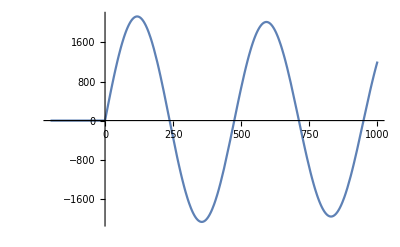

```mathematica
a1=Plot[αα[t/atomicunitoftime,4/3 π(1*nanometer)^3],{t,-200,1000}]
```

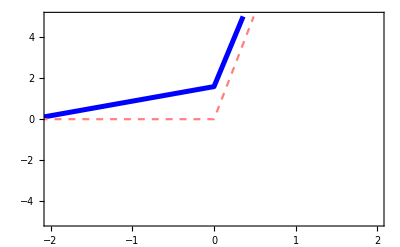

```mathematica
a2=ListLinePlot[{alft, aalf}, PlotStyle->{Directive[Blue,Thickness[0.009]],Directive[Pink,Dashed, Thickness[0.004]]}, Frame->True,PlotRange->{{-2,2},{-5,5}}]
```

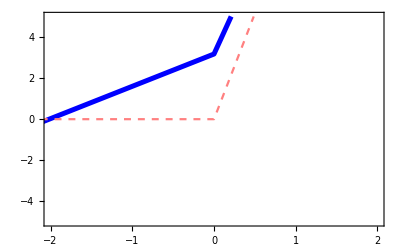

```mathematica
a3=ListLinePlot[{alft, aalf}, PlotStyle->{Directive[Blue,Thickness[0.009]],Directive[Pink,Dashed, Thickness[0.004]]}, Frame->True,PlotRange->{{-2,2},{-5,5}}]
```

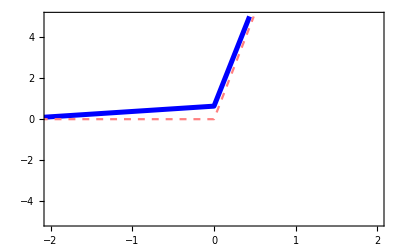

```mathematica
a4=ListLinePlot[{alft, aalf}, PlotStyle->{Directive[Blue,Thickness[0.009]],Directive[Pink,Dashed, Thickness[0.004]]}, Frame->True,PlotRange->{{-2,2},{-5,5}}]
```

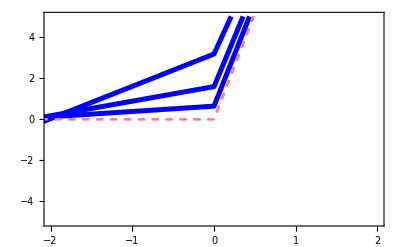

```mathematica
Show[a2,a3,a4]
```

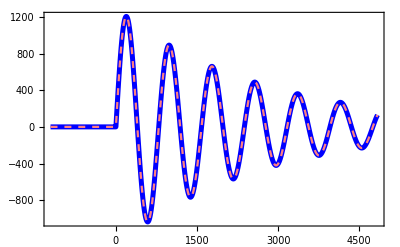

```mathematica
ListLinePlot[{alft, aalf}, PlotStyle->{Directive[Blue,Thickness[0.009]],Directive[Pink,Dashed, Thickness[0.004]]}, Frame->True,PlotRange->Automatic]
```

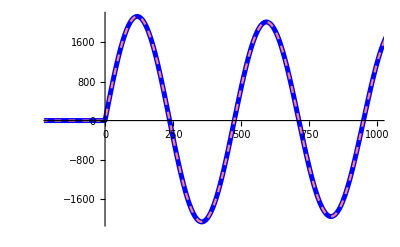

```mathematica
Show[a1,a2]
```

```mathematica
num=2^17;
range=100; (*freq in eV*)
αArray={};
For[i=1,i≤6,i++,
AppendTo[αArray,Interpolation[Re[αdata[num, range, ϵDrudeAl, αPol, 4/3 π(1*nanometer)^3,i]]]]
]
```

```mathematica
num=2^18;
range=850; (*freq in eV*)
αArrayWerner={};
For[i=1,i≤6,i++,
AppendTo[αArrayWerner,Interpolation[Re[αdata[num, range, ϵWernerAu, αPol, 4/3 π(1*nanometer)^3,i]]]]
]//Timing
```

{440.178,Null}

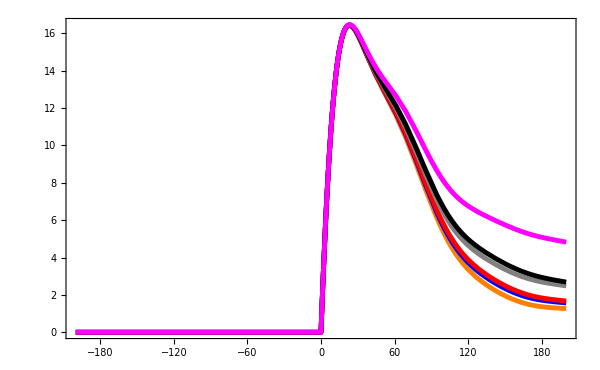

PolarizabilityCausalityWernerAu.pdf

```mathematica
Plot[
{αArrayWerner[[1]][t/atomicunitoftime]*SIunitofpolarizability,αArrayWerner[[2]][t/atomicunitoftime]*SIunitofpolarizability,αArrayWerner[[3]][t/atomicunitoftime]*SIunitofpolarizability,αArrayWerner[[4]][t/atomicunitoftime]*SIunitofpolarizability,αArrayWerner[[5]][t/atomicunitoftime]*SIunitofpolarizability,αArrayWerner[[6]][t/atomicunitoftime]*SIunitofpolarizability},{t,-200,200},
PlotRange->{{-200,200},All},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
Axes->False,
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{icosahedron}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Solid shape}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.23,0.55}],
ImageSize->600]
Export["PolarizabilityCausalityWernerAu.pdf",%]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["PolarizabilityCausalityWernerAu.pdf"]]]
```

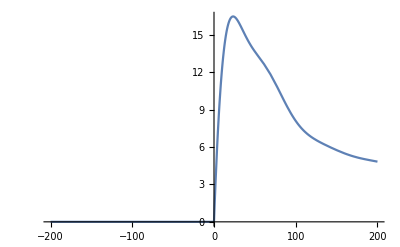

```mathematica
Plot[αArrayWerner[[6]][t/atomicunitoftime]*SIunitofpolarizability,{t,-200,200}]
```

```mathematica
num=2^17;
range=100; (*freq in eV*)
αArrayTaylor={};
For[i=1,i≤6,i++,
AppendTo[αArrayTaylor,Interpolation[Re[αdata[num, range, ϵDrudeAl, αPolTaylor, 4/3 π(1*nanometer)^3,i]]]]
]
```

```mathematica
num=2^17;
range=100; (*freq in eV*)
αArrayTetra={};
For[i=1,i≤7,i++,
AppendTo[αArrayTetra,Interpolation[Re[αdata[num, range, ϵDrudeAl, αPolTetra, 4/3 π(1*nanometer)^3,i]]]]
]
```

```mathematica
alfaPlatonicDrudeAl={};
For[i=1,i≤6,i++,
AppendTo[alfaPlatonicDrudeAl,ParallelTable[{t*atomicunitoftime,αArray[[i]][t]*SIunitofpolarizability},{t,-50,200,0.1}]]
]
Export["alfaPlatonicDrudeAl.mx",alfaPlatonicDrudeAl]
```

alfaPlatonicDrudeAl.mx

```mathematica
alfaPlatonicWernerAu={};
For[i=1,i≤6,i++,
AppendTo[alfaPlatonicWernerAu,Table[{t*atomicunitoftime,αArrayWerner[[i]][t]*SIunitofpolarizability},{t,-50,200,0.1}]]
]
Export["alfaPlatonicWernerAu.mx",alfaPlatonicWernerAu]
```

alfaPlatonicWernerAu.mx

```mathematica
alfttTaylor={};
For[i=1,i≤6,i++,
AppendTo[alfttTaylor,ParallelTable[{t*atomicunitoftime,αArrayTaylor[[i]][t]*SIunitofpolarizability[[1]]},{t,-50,200,0.1}]]
]
```

```mathematica
alfttTetra={};
For[i=1,i≤6,i++,
AppendTo[alfttTetra,ParallelTable[{t*atomicunitoftime,αArrayTetra[[i]][t]*SIunitofpolarizability[[1]]},{t,-50,200,0.1}]]
]
```

```mathematica
alfaPlatonicDrudeAl=Import["alfaPlatonicDrudeAl.mx"];
alfaPlatonicWernerAu=Import["alfaPlatonicWernerAu.mx"];
```

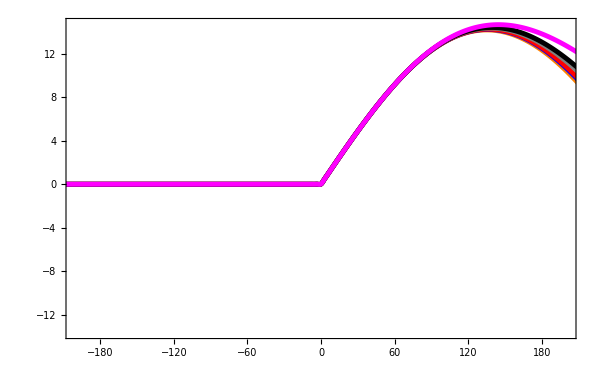

```mathematica
ListLinePlot[
alfaPlatonicDrudeAl,
InterpolationOrder->3,
PlotRange->{{-200,200},Automatic},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
Axes->False,
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{icosahedron}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Solid shape}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.83,0.35}],
ImageSize->600]
Export["PolarizabilityCausality.pdf",%]
```

```mathematica
αArrayWerner[[1]][t]
```

InterpolatingFunction[{{-4117.69, 4117.75}}, <>][t]

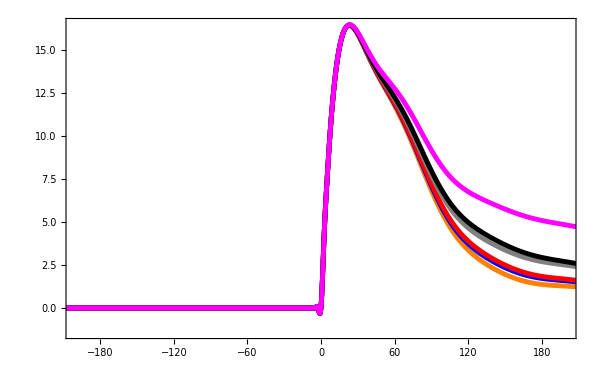

PolarizabilityCausalityWernerAu.pdf

```mathematica
ListLinePlot[
alfaPlatonicWernerAu,
InterpolationOrder->3,
PlotRange->{{-200,200},All},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
Axes->False,
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{icosahedron}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Solid shape}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.23,0.55}],
ImageSize->600]
Export["PolarizabilityCausalityWernerAu.pdf",%]
```

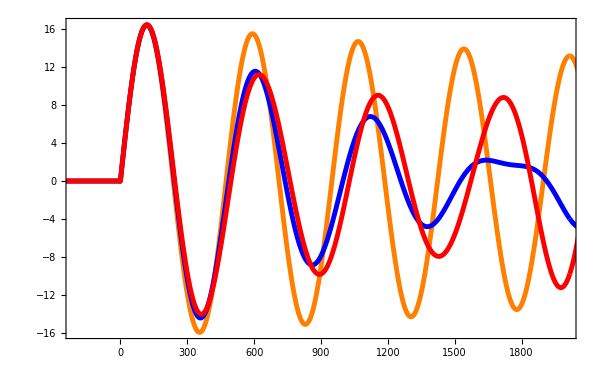

```mathematica
ListLinePlot[
{alftt[[1]],alftt[[2]],alftt[[3]]},
InterpolationOrder->3,
PlotRange->{{-200,2000},Automatic},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{icosahedron}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.8,0.19}],
ImageSize->600]
```

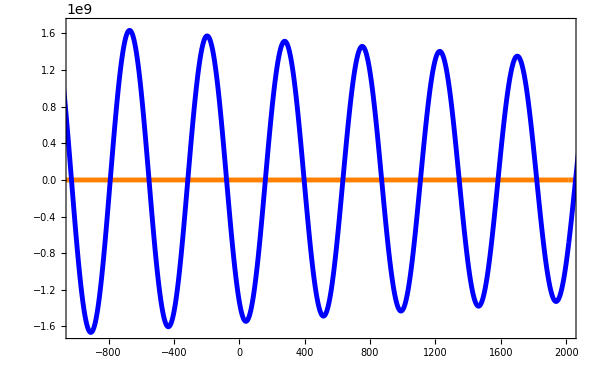

```mathematica
ListLinePlot[
{alftt[[3]],alfttTaylor[[6]]},
InterpolationOrder->3,
PlotRange->{{-1000,2000},Automatic},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{icosahedron}","\\text{icosahedron Taylor}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.8,0.19}],
ImageSize->600]
```

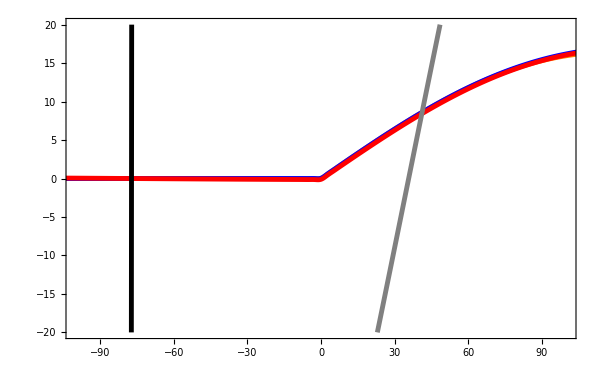

```mathematica
ListLinePlot[
{alfttTetra[[1]],alfttTetra[[2]], alfttTetra[[3]], alfttTetra[[4]],alfttTetra[[5]]},
InterpolationOrder->3,
PlotRange->{{-100,100},{-20,20}},
Frame->True,
FrameLabel->{MaTeX["\\text{Time}\\text{ [as]}",FontSize->25],MaTeX["\\alpha (10^{-11} m^3/s)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{lineal}","\\text{tercer}","\\text{cuarto}","\\text{quinto}","\\text{sexto}","\\text{séptimo}"},FontSize->20],
LegendLabel->MaTeX["\\text{Dielectric function}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.83,0.24}],
ImageSize->600]
```

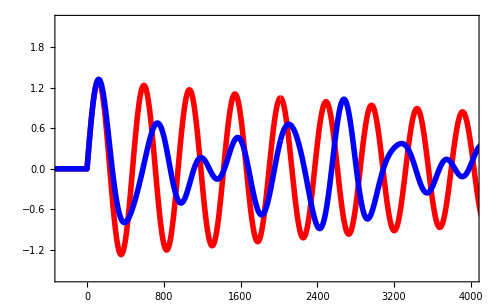

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->20};

padding={{80,1},{80,1}};
a2=ListPlot[{alft[[1]],alft[[5]]},

Joined->True,
PlotRange->{{-250,4000},{-1.6,2.2}},ImagePadding->padding,

InterpolationOrder->3,
PlotStyle->{{Red,Thickness[0.008]},{Blue,Thickness[0.008]}},
FrameStyle->Directive[Thickness[0.003]],
FrameTicksStyle->Directive[Black,Thickness[0.003]],


FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},

PlotLegends->Placed[SwatchLegend[MaTeX[{"\\text{sphere}","\\text{cube}"},Magnification->1.53],LegendMarkerSize->{25,6},
LegendLabel->Column[MaTeX[{},Magnification->1.53],Center],
LegendFunction->(Framed[#,RoundingRadius->3,Background->White,FrameStyle->{Black},FrameMargins->1]&),
LegendMargins->5,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman", 10],Spacings->0.5],{0.87,0.81}],


FrameLabel->MaTeX[{"\\text{Time (as)}","\\alpha_s  \\, (10^{-11} \\; \\text{m}^3/\\text{s})"},Magnification->1.85],


Frame->True,
GridLines->None,
GridLinesStyle->Directive[Gray,Dotted,Thickness[0.0001]],

BaseStyle->texStyle,
ImageSize->{499.8,Automatic}]
```

#### Poles of α for a cube. Comparison with Fuchs.

```mathematica
DeleteCases[resonancesωPlatonicSolids[ϵDrudeAl,sphere],x_/;x<1]
```

```mathematica
resonancesωPlatonicSolids[ϵDielecFunc_,polyhedronType_]:=Module[{ϵ=ϵDielecFunc,polyhedron=polyhedronType},
(*Calculating the poles of the polarizability α*)
Switch[polyhedron,
sphere,DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]+2==0,ω],x_/;x<1]//Sort,
icosahedron,DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]^3+5.29169 ϵ[ω]^2+8.52687ϵ[ω]+4.0896==0,ω],x_/;x<1]//Sort,
dodecahedron,DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]^3+4.72932 ϵ[ω]^2+6.53464ϵ[ω]+2.56842==0,ω],x_/;x<1]//Sort,
octahedron, DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]^4+8.26227 ϵ[ω]^3+19.8267 ϵ[ω]^2+15.6191ϵ[ω]+3.5507==0,ω],x_/;x<1]//Sort,
hexahedron,DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]^4+8.0341 ϵ[ω]^3+19.3534 ϵ[ω]^2+15.4349ϵ[ω]+3.6442==0,ω],x_/;x<1]//Sort,
tetrahedron,DeleteCases[Re[ω/electronVolt]/.NSolve[ϵ[ω]^4+14.1983 ϵ[ω]^3+44.9182 ϵ[ω]^2+30.2668ϵ[ω]+5.0285==0,ω],x_/;x<1]//Sort
]]
resonancesPlatonicSolids[polyhedronType_]:=Module[{polyhedron=polyhedronType},
(*Calculating the poles of the polarizability α*)
Switch[polyhedron,
sphere,ϵ/.NSolve[ϵ+2==0,ϵ]//Sort,
icosahedron,ϵ/.NSolve[ϵ^3+5.29169 ϵ^2+8.52687ϵ+4.0896==0,ϵ]//Sort,
dodecahedron,ϵ/.NSolve[ϵ^3+4.72932 ϵ^2+6.53464ϵ+2.56842==0,ϵ]//Sort,
octahedron, ϵ/.NSolve[ϵ^4+8.26227 ϵ^3+19.8267 ϵ^2+15.6191ϵ+3.5507==0,ϵ]//Sort,
hexahedron,ϵ/.NSolve[ϵ^4+8.0341 ϵ^3+19.3534 ϵ^2+15.4349ϵ+3.6442==0,ϵ]//Sort,
tetrahedron,ϵ/.NSolve[ϵ^4+14.1983 ϵ^3+44.9182 ϵ^2+30.2668ϵ+5.0285==0,ϵ]//Sort
]]
```

```mathematica
resonancesPlatonicSolids[icosahedron]
resonancesPlatonicSolids[dodecahedron]
```

{-2.67753,-1.73262,-0.881545}

{-2.58743,-1.46371,-0.678174}

```mathematica
resonancesPlatonicSolids[hexahedron]
resonancesPlatonicSolids[octahedron]
```

{-4.36993,-2.43073,-0.809769,-0.423672}

{-4.74324,-2.29519,-0.831679,-0.392161}

```mathematica
resonancesωPlatonicSolids[ϵDrudeAl,hexahedron]
```

{5.67037,7.09458,9.7685,11.0138}

```mathematica
resonancesPlatonicSolids[hexahedron]
```

{-4.36993,-2.43073,-0.809769,-0.423672}

## Linear Momentum Transfer

```mathematica
fz[ω_,v_,b_,Vol_,αα_, ϵϵ_, polyhedronType_]:=((2*qElectronCharge^2*ω^3)/(π*v^5*(γLorentz[v])^3))*(2γLorentz[v]*Im[αα[ω,ϵϵ,Vol, polyhedronType]](BesselK[1,(ω*b)/(v*γLorentz[v])]^2+1/γLorentz[v]^2*BesselK[0,(ω*b)/(v*γLorentz[v])]^2))
fx[ω_,v_,b_,Vol_,αα_, ϵϵ_, polyhedronType_]:=((2*qElectronCharge^2*ω^3)/(π*v^5*(γLorentz[v])^3))*(2*Re[αα[ω,ϵϵ,Vol, polyhedronType]](BesselK[1,(ω*b)/(v*γLorentz[v])]*BesselK[0,(ω*b)/(v*γLorentz[v])]+(v*γLorentz[v])/(ω*b)BesselK[1,(ω*b)/(v*γLorentz[v])]^2+1/γLorentz[v]^2*BesselK[1,(ω*b)/(v*γLorentz[v])]*BesselK[0,(ω*b)/(v*γLorentz[v])]))
```

```mathematica
Fx[v_,b_,Vol_,αα_,ϵϵ_, polyhedronType_]:=NIntegrate[fx[ω,v,b,Vol,αα, ϵϵ, polyhedronType],{ω,0,∞}, Method->"DoubleExponential"]
Fz[v_,b_,Vol_,αα_,ϵϵ_, polyhedronType_]:=NIntegrate[fz[ω,v,b,Vol,αα, ϵϵ, polyhedronType],{ω,0,∞}, Method->"DoubleExponential"]
```

```mathematica
polyhedron=sphere;
labels={"sphere", "icosahedron", "dodecahedron", "octahedron", "hexahedron", "tetrahedron"};
FxsmallvPlatonicSolids={};

For[polyhedron = sphere,polyhedron ≤ tetrahedron,polyhedron++,
AppendTo[FxsmallvPlatonicSolids,ParallelTable[{v,10^28 Fx[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]*SIunitofmomentum},{v,0.1,0.99,0.00445}]]];
```

```mathematica
Export["FxsmallvPlatonicSolids.mx", FxsmallvPlatonicSolids]
```

FxsmallvPlatonicSolids.mx

```mathematica
FxsmallvPlatonicSolids=Import["FxsmallvPlatonicSolids.mx"];
```

```mathematica
Import["FxsmallvPlatonicSolids.mx"]==Fxsmallv
```

True

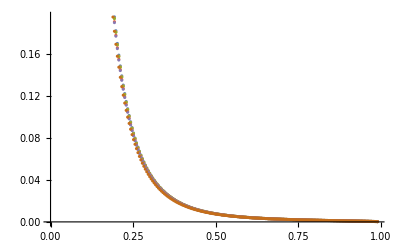

-Graphics-

```mathematica
ListPlot[Fxsmallv]
ListPlot[Import["FxsmallvPlatonicSolids.mx"]]
```

```mathematica
polyhedron=sphere;
Fzsmallv=ParallelTable[{v,10^28 Fz[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]*SIunitofmomentum},{v,0.1,0.99,0.00445}];
```

```mathematica
ListPlot[Fxsmallv, PlotRange->All]
```

-Graphics-

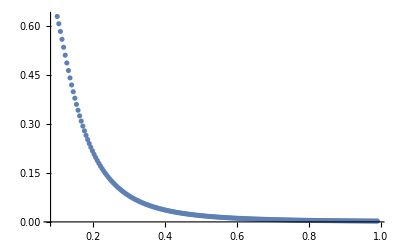

```mathematica
ListPlot[Fzsmallv, PlotRange->All]
```

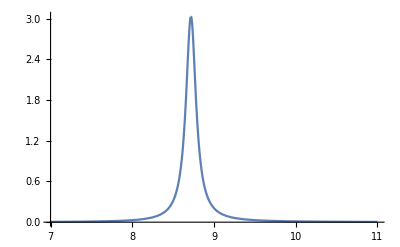

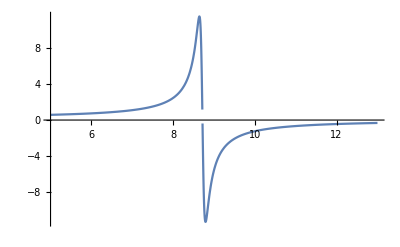

```mathematica
Plot[10^44*fz[ω*electronVolt, 0.5*cSpeedLight, 1.5*nanometer, 4/3 π*(1*nanometer)^3,αPol, ϵDrudeAl, sphere]*SIunitofforce*(atomicunitoftime*attosec)^2,{ω,7,11}, PlotRange->All]
Plot[10^44*fx[ω*electronVolt, 0.5*cSpeedLight, 1.5*nanometer, 4/3 π*(1*nanometer)^3,αPol, ϵDrudeAl, sphere]*SIunitofforce*(atomicunitoftime*attosec)^2,{ω,5,13}, PlotRange->All]
```

## Angular Momentum Transfer

### Definitions

```mathematica
τ[ω_,v_,b_,Vol_,αα_, ϵϵ_, polyhedronType_]:=-((8*qElectronCharge^2*ω^2)/(Pi*v^4*(γLorentz[v])^3))*BesselK[0,(ω*b)/(v*γLorentz[v])]*BesselK[1,(ω*b)/(v*γLorentz[v])]*(Im[αα[ω,ϵϵ,Vol, polyhedronType]])
L[v_,b_,Vol_,αα_,ϵϵ_, polyhedronType_]:=(-1)*NIntegrate[τ[ω,v,b,Vol,αα, ϵϵ, polyhedronType],{ω,0,∞}, Method->"DoubleExponential"]
```

```mathematica
τIso[ω_,v_,b_,Vol_,αα_, ϵϵ_, ellipsoidType_, eccentricity_]:=-((4*qElectronCharge^2*ω^2)/(Pi*v^4*(γLorentz[v])^3))*BesselK[0,(ω*b)/(v*γLorentz[v])]*BesselK[1,(ω*b)/(v*γLorentz[v])]*(Im[ αα[ω,ϵϵ,Vol, ellipsoidType, eccentricity][[2]] + αα[ω,ϵϵ,Vol, ellipsoidType, eccentricity][[3]] ])
LIso[v_,b_,Vol_,αα_,ϵϵ_, ellipsoidType_, eccentricity_]:=
(-1)*NIntegrate[τIso[ω,v,b,Vol,αα, ϵϵ, ellipsoidType, eccentricity],{ω,0,∞}, Method->"DoubleExponential"]
```

```mathematica
τx[ω_,v_,b_,Vol_,αα_, ϵϵ_, angleTheta_, eccentricity_]:=((4*qElectronCharge^2*ω^2)/(Pi*v^4*(γLorentz[v])^4))(BesselK[0,(ω*b)/(v*γLorentz[v])]^2*Re[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[2,3]]]+γLorentz[v]*BesselK[0,(ω*b)/(v*γLorentz[v])]*BesselK[1,(ω*b)/(v*γLorentz[v])]*Im[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[2,1]]])
τy[ω_,v_,b_,Vol_,αα_, ϵϵ_, angleTheta_, eccentricity_]:=((4*qElectronCharge^2*ω^2)/(Pi*v^4*(γLorentz[v])^4))(γLorentz[v]^2*BesselK[1,(ω*b)/(v*γLorentz[v])]^2*Re[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[3,1]]]-BesselK[0,(ω*b)/(v*γLorentz[v])]^2*Re[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[1,3]]]-γLorentz[v]*BesselK[0,(ω*b)/(v*γLorentz[v])]*BesselK[1,(ω*b)/(v*γLorentz[v])]*Im[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[1,1]] + αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[3,3]]])
τz[ω_,v_,b_,Vol_,αα_, ϵϵ_, angleTheta_, eccentricity_]:=((4*qElectronCharge^2*ω^2)/(Pi*v^4*(γLorentz[v])^3))(BesselK[0,(ω*b)/(v*γLorentz[v])]*BesselK[1,(ω*b)/(v*γLorentz[v])]*Im[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[2,3]]]-γLorentz[v]*BesselK[1,(ω*b)/(v*γLorentz[v])]^2*Re[αα[ω,ϵϵ,Vol, angleTheta, eccentricity][[2,1]]])
```

### Platonic Solids

```mathematica
For[polyhedron=sphere, polyhedron≤tetrahedron, polyhedron++,
WriteString["stdout",labels[[polyhedron]],"\n"];
For[i=1,res=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron];i≤Length[res],i++,
WriteString["stdout",StringJoin["ω",ToString[i], "= ", ToString[res[[i]]], " eV, "]]
];
WriteString["stdout","\n\n"];
]
```

sphere
ω1= 7.5869 eV, 

icosahedron
ω1= 6.85233 eV, ω2= 7.94948 eV, ω3= 9.58035 eV, 

dodecahedron
ω1= 6.93786 eV, ω2= 8.37214 eV, ω3= 10.1443 eV, 

octahedron
ω1= 5.48293 eV, ω2= 7.23904 eV, ω3= 9.70989 eV, ω4= 11.1378 eV, 

hexahedron
ω1= 5.67037 eV, ω2= 7.09458 eV, ω3= 9.7685 eV, ω4= 11.0138 eV, 

tetrahedron
ω1= 3.96002 eV, ω2= 6.30182 eV, ω3= 10.4264 eV, ω4= 11.7307 eV,

```mathematica
resonancesωPlatonicSolids[ϵDrudeAl,tetrahedron]
```

{3.96002,6.30182,10.4264,11.7307}

```mathematica
labels
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

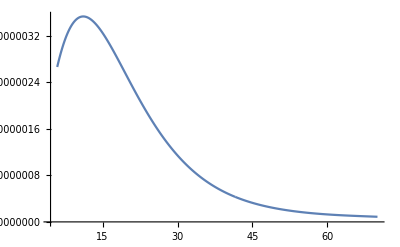

```mathematica
ListLinePlot[τysmallvPlatonicSolids[[3]][[2]], PlotRange->All]
```

```mathematica
Export["τysmallvPlatonicSolids.mx", τysmallvPlatonicSolids]
```

τysmallvPlatonicSolids.mx

```mathematica
τysmallvPlatonicSolids=Import["τysmallvPlatonicSolids.mx"];
```

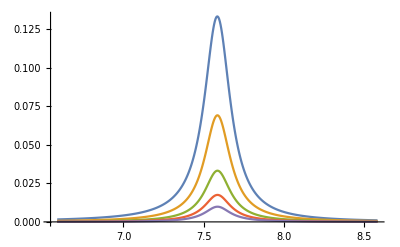
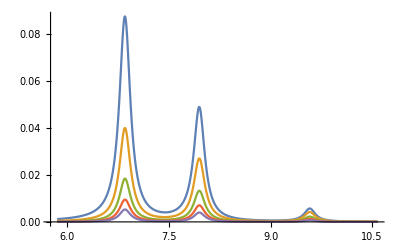
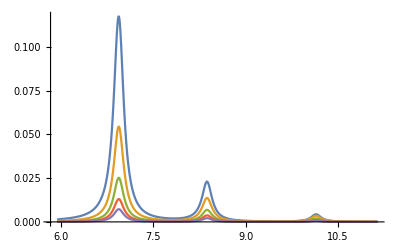
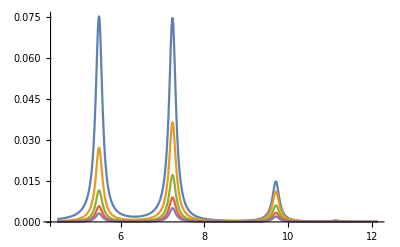
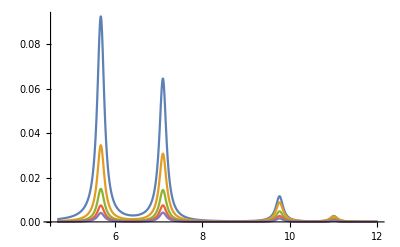
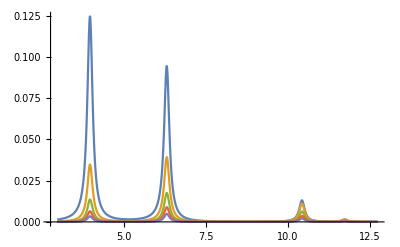

```mathematica
plots=Table[ListLinePlot[τysmallvPlatonicSolids[[i]], PlotRange->All],{i,sphere,tetrahedron}]
```

#### Spectral densities

```mathematica
labels
```

{sphere,icosahedron,dodecahedron,octahedron,hexahedron,tetrahedron}

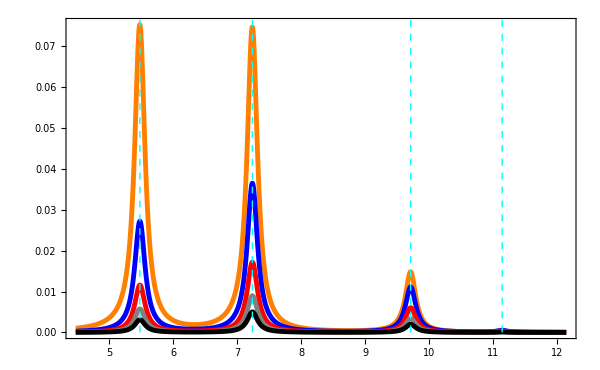

```mathematica
solid = octahedron;
Nres=Length[resonancesωPlatonicSolids[ϵDrudeAl,solid]];
Res1=resonancesωPlatonicSolids[ϵDrudeAl,solid][[1]];
Res2=resonancesωPlatonicSolids[ϵDrudeAl,solid][[ Min[2,Nres] ]];
Res3=resonancesωPlatonicSolids[ϵDrudeAl,solid][[ Min[3,Nres] ]];
Res4=resonancesωPlatonicSolids[ϵDrudeAl,solid][[ Min[4,Nres] ]];

lineStyle={Thick,Cyan,Dashed};
maxy=Max[τysmallvPlatonicSolids[[solid]]/.{x_,y_}->y];
line1=Line[{{Res1,0},{Res1,1.1*maxy}}];
line2=Line[{{Res2,0},{Res2,1.1*maxy}}];
line3=Line[{{Res3,0},{Res3,1.1*maxy}}];
line4=Line[{{Res4,0},{Res4,1.1*maxy}}];

ListLinePlot[
τysmallvPlatonicSolids[[solid]],
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLabel->labels[[solid]],
PlotLegends->Placed[LineLegend[MaTeX[{"0.1","0.2","0.3","0.4","0.5","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["v/c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.93,0.7}],
ImageSize->600,Epilog->{Directive[lineStyle],line1,line2,line3,line4}]
```

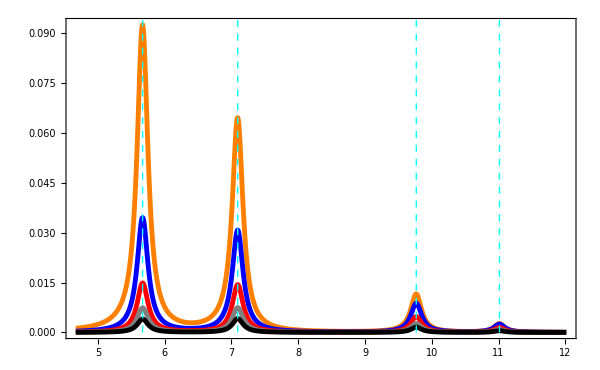

```mathematica
solid = hexahedron;
Nres=Length[resonancesωPlatonicSolids[ϵDrudeAl,solid]];
Res1=resonancesωPlatonicSolids[ϵDrudeAl,solid][[1]];
Res2=resonancesωPlatonicSolids[ϵDrudeAl,solid][[ Min[2,Nres] ]];
Res3=resonancesωPlatonicSolids[ϵDrudeAl,solid][[ Min[3,Nres] ]];
Res4=resonancesωPlatonicSolids[ϵDrudeAl,solid][[ Min[4,Nres] ]];

lineStyle={Thick,Cyan,Dashed};
maxy=Max[τysmallvPlatonicSolids[[solid]]/.{x_,y_}->y];
line1=Line[{{Res1,0},{Res1,1.1*maxy}}];
line2=Line[{{Res2,0},{Res2,1.1*maxy}}];
line3=Line[{{Res3,0},{Res3,1.1*maxy}}];
line4=Line[{{Res4,0},{Res4,1.1*maxy}}];

ListLinePlot[
τysmallvPlatonicSolids[[solid]],
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLabel->labels[[solid]],
PlotLegends->Placed[LineLegend[MaTeX[{"0.1","0.2","0.3","0.4","0.5","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["v/c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.93,0.7}],
ImageSize->600,Epilog->{Directive[lineStyle],line1,line2,line3,line4}]
```

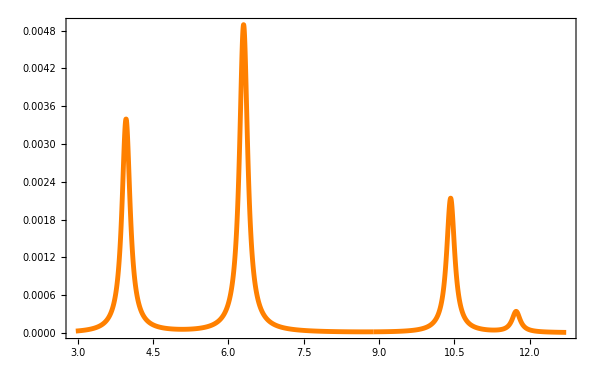

```mathematica
ListLinePlot[
τysmallvPlatonicSolids[[tetrahedron]][[5]],
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLabel->labels[[tetrahedron]],
(*PlotLegends->Placed[LineLegend[MaTeX[{"0.1","0.2","0.3","0.4","0.5","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["v/c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.93,0.7}],*)
ImageSize->600]
```

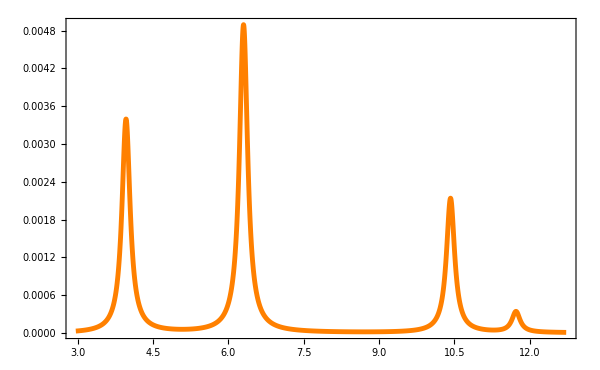

```mathematica
vv=0.5*cSpeedLight;
bb=3.5*nanometer;
VVol=4/3 π(1*nanometer)^3;
ϵϵϵ=ϵDrudeAl;
polyhedron=tetrahedron;
polyhedron2=sphere;

Nres=Length[resonancesωPlatonicSolids[ϵDrudeAl,polyhedron]];
Res1=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[1]];
Res2=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[2,Nres] ]];
Res3=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[3,Nres] ]];
Res4=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[4,Nres] ]];
ωmin=Min[Res1,Res2,Res3,Res4]-1;
ωmax=Max[Res1,Res2,Res3,Res4]+1;

Plot[
-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, polyhedron],{ω,ωmin,ωmax},
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
(*PlotLabel->labels[[tetrahedron]],
PlotLegends->Placed[LineLegend[MaTeX[{"0.1","0.2","0.3","0.4","0.5","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["v/c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.93,0.7}],*)
ImageSize->600]
```

```mathematica
ListContourPlot
```

```mathematica
labels
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

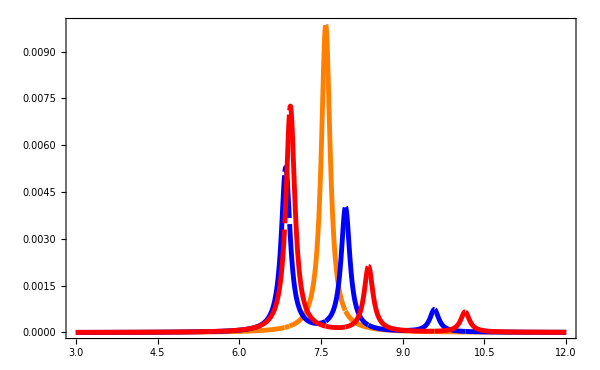

SpectralDensities-IcoDodeca2.pdf

```mathematica
vv=0.5*cSpeedLight;
bb=3.5*nanometer;
VVol=4/3 π(1*nanometer)^3;
ϵϵϵ=ϵDrudeAl;
polyhedron=icosahedron;

Nres=Length[resonancesωPlatonicSolids[ϵDrudeAl,polyhedron]];
Res1=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[1]];
Res2=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[2,Nres] ]];
Res3=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[3,Nres] ]];
Res4=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[4,Nres] ]];
Nres2=Length[resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1]];
Res5=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[1]];
Res6=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[ Min[2,Nres2] ]];
Res7=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[ Min[3,Nres2] ]];
Res8=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[ Min[4,Nres2] ]];

ωmin=Min[Res1,Res2,Res3,Res4,Res5,Res6,Res7,Res8]-1;
ωmax=Max[Res1,Res2,Res3,Res4,Res5,Res6,Res7,Res8]+1;

τarrayIcosahedron ={-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, sphere],-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, polyhedron],-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, polyhedron+1]};

in=icosahedron;fin=dodecahedron;
Plot[
τarrayIcosahedron,
{ω,3,12},
PlotRange->{{3,12},All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[icosahedron]],AbsoluteThickness[3.5]},{color[[dodecahedron]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
(*PlotLabel->labels[[tetrahedron]],*)
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{Sphere}", "\\text{Icosahedron}", "\\text{Dodecahedron}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.83,0.7}],
ImageSize->600]
Export["SpectralDensities-IcoDodeca2.pdf",%]
```

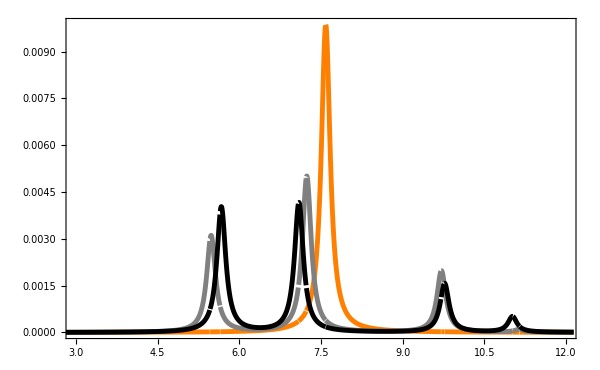

SpectralDensities-OctaHexa.pdf

```mathematica
vv=0.5*cSpeedLight;
bb=3.5*nanometer;
VVol=4/3 π(1*nanometer)^3;
ϵϵϵ=ϵDrudeAl;
polyhedron=octahedron;

Nres=Length[resonancesωPlatonicSolids[ϵDrudeAl,polyhedron]];
Res1=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[1]];
Res2=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[2,Nres] ]];
Res3=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[3,Nres] ]];
Res4=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[4,Nres] ]];
Nres2=Length[resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1]];
Res5=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[1]];
Res6=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[ Min[2,Nres2] ]];
Res7=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[ Min[3,Nres2] ]];
Res8=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron+1][[ Min[4,Nres2] ]];

ωmin=Min[Res1,Res2,Res3,Res4,Res5,Res6,Res7,Res8]-1;
ωmax=Max[Res1,Res2,Res3,Res4,Res5,Res6,Res7,Res8]+1;

τarrayIcosahedron ={-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, sphere],-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, polyhedron],-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, polyhedron+1]};

Plot[
τarrayIcosahedron,
{ω,2,ωmax},
PlotRange->{{3,12},All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[sphere]],AbsoluteThickness[3.5]},{color[[octahedron]],AbsoluteThickness[3.5]},{color[[hexahedron]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
(*PlotLabel->labels[[tetrahedron]],*)
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{Sphere}", "\\text{Octahedron}", "\\text{Hexahedron}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.83,0.7}],
ImageSize->600]
Export["SpectralDensities-OctaHexa.pdf",%]
```

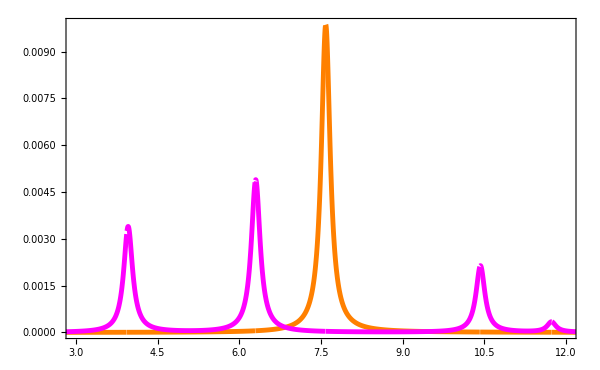

SpectralDensities-Tetra.pdf

```mathematica
vv=0.5*cSpeedLight;
bb=3.5*nanometer;
VVol=4/3 π(1*nanometer)^3;
ϵϵϵ=ϵDrudeAl;
polyhedron=tetrahedron;

Nres=Length[resonancesωPlatonicSolids[ϵDrudeAl,polyhedron]];
Res1=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[1]];
Res2=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[2,Nres] ]];
Res3=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[3,Nres] ]];
Res4=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron][[ Min[4,Nres] ]];

ωmin=Min[Res1,Res2,Res3,Res4]-1;
ωmax=Max[Res1,Res2,Res3,Res4]+1;

τarrayIcosahedron ={-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, sphere],-τ[ω*electronVolt,vv,bb,VVol,αPol, ϵϵϵ, polyhedron]};

Plot[
τarrayIcosahedron,
{ω,2,ωmax},
PlotRange->{{3,12},All},
Frame->True,
FrameLabel->{MaTeX["\\hbar \\omega \\text{ [eV]}",FontSize->25],MaTeX["\\mathcal{L}(\\omega)",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[sphere]],AbsoluteThickness[3.5]},{color[[tetrahedron]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
(*PlotLabel->labels[[tetrahedron]],*)
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{Sphere}", "\\text{Tetrahedron}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.83,0.7}],
ImageSize->600]
Export["SpectralDensities-Tetra.pdf",%]
```

```mathematica
labels
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
resonancesωPlatonicSolids[ϵDrudeAl,icosahedron]
```

{6.85233,7.94948,9.58035}

```mathematica
LysmallvPlatonicSolids={};

For[polyhedron = sphere,polyhedron ≤ tetrahedron,polyhedron++,
AppendTo[LysmallvPlatonicSolids,Table[{v,10^3 L[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]},{v,0.1,0.99,0.00445}]]];
```

```mathematica
LysmallbPlatonicSolids={};

For[polyhedron = sphere,polyhedron ≤ tetrahedron,polyhedron++,
AppendTo[LysmallbPlatonicSolids,Table[{b,10^3 L[0.5*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]},{b,3,10,0.035}]]];
```

```mathematica
LysmallvPlatonicSolidsToSphere={};

For[polyhedron = sphere,polyhedron ≤ tetrahedron,polyhedron++,
AppendTo[LysmallvPlatonicSolidsToSphere,Table[{v,10*(L[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]-L[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, sphere])/L[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, sphere]},{v,0.1,0.99,0.00445}]]]; //Timing
```

{78.0679,Null}

```mathematica
LysmallbPlatonicSolidsToSphere={};

For[polyhedron = sphere,polyhedron ≤ tetrahedron,polyhedron++,
AppendTo[LysmallbPlatonicSolidsToSphere,Table[{b,10*(L[0.5*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]-L[0.5*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, sphere])/L[0.5*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, sphere]},{b,3,10,0.035}]]]; //Timing
```

{74.7519,Null}

```mathematica
Export["LysmallvPlatonicSolids.mx", LysmallvPlatonicSolids]
Export["LysmallbPlatonicSolids.mx", LysmallbPlatonicSolids]
```

LysmallvPlatonicSolids.mx

LysmallbPlatonicSolids.mx

```mathematica
Export["LysmallvPlatonicSolidsToSphere.mx", LysmallvPlatonicSolidsToSphere]
Export["LysmallbPlatonicSolidsToSphere.mx", LysmallbPlatonicSolidsToSphere]
```

LysmallvPlatonicSolidsToSphere.mx

LysmallbPlatonicSolidsToSphere.mx

```mathematica
LysmallvPlatonicSolids=Import["LysmallvPlatonicSolids.mx"];
LysmallbPlatonicSolids=Import["LysmallbPlatonicSolids.mx"];
LysmallvPlatonicSolidsToSphere=Import["LysmallvPlatonicSolidsToSphere.mx"];
LysmallbPlatonicSolidsToSphere=Import["LysmallbPlatonicSolidsToSphere.mx"];
```

```mathematica
labels
```

{Sphere,Icosahedron,Dodecahedron,Octahedron,Hexahedron,Tetrahedron}

```mathematica
marker[Red,5]
```

-Graphics-

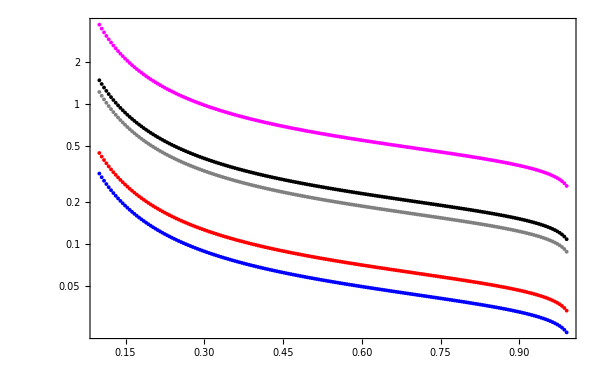

LysmallvPlatonicSolidsToSphere.pdf

```mathematica
ListLogPlot[
LysmallvPlatonicSolidsToSphere[[2;;]],
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
Mesh->5,
FrameLabel->{MaTeX["v/c",FontSize->25],MaTeX["\\big(\\Delta L_p - \\Delta L_s\\big)\\big/\\Delta L_s  ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{icosahedron}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.84,0.78}],
ImageSize->600]
Export["LysmallvPlatonicSolidsToSphere.pdf",%]
```

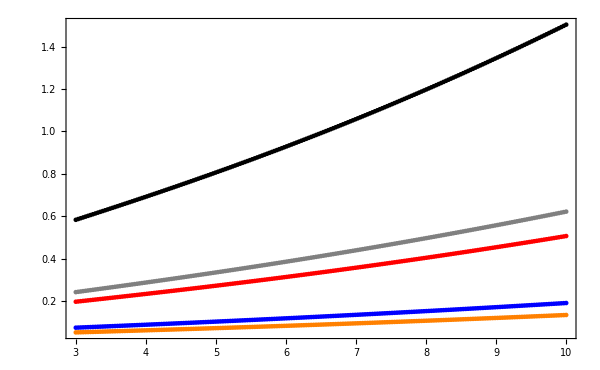

LysmallbPlatonicSolidsToSphere.pdf

```mathematica
ListPlot[
LysmallbPlatonicSolidsToSphere[[2;;]],
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["b\\text{ [nm]}",FontSize->25],MaTeX["\\big(\\Delta L_p - \\Delta L_s\\big)\\big/\\Delta L_s  ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{icosahedron}","\\text{dodecahedron}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.15,0.72}],
ImageSize->600]
Export["LysmallbPlatonicSolidsToSphere.pdf",%]
```

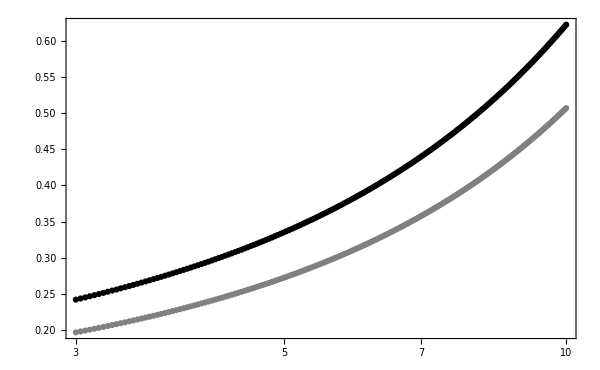

LysmallbPlatonicSolidsOH.pdf

```mathematica
in=4;fin=5;
ListLogLinearPlot[
LysmallbPlatonicSolidsToSphere[[in;;fin]],
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["b\\text{ [nm]}",FontSize->25],MaTeX["\\big(\\Delta L_p - \\Delta L_s\\big)\\big/\\Delta L_s  ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[in]],AbsoluteThickness[3.5]},{color[[fin]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[labels[[in;;fin]],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.85,0.22}],
ImageSize->600]
Export["LysmallbPlatonicSolidsOH.pdf",%]
```

```mathematica
{1,2,3}[[2;;3]]
```

{2,3}

```mathematica
LysmallPlatonicSolids={};

For[polyhedron = sphere,polyhedron ≤ tetrahedron,polyhedron++,
AppendTo[LysmallPlatonicSolids,Table[{v,b,10^3 L[v*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]},{v,0.1,0.99,0.00445},{b,3,10,0.035}]]]; //Timing
```

$Aborted

```mathematica
t1=Table[{v,b,10^3 L[v*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, sphere]},{v,0.1,0.99,0.1},{b,3,10,1}];
```

```mathematica
ListContourPlot[Table[{x,y,x*y},{x,-1,1,0.01},{y,-1,1,0.01}]]
```

-Graphics-

```mathematica
data=Table[{v=RandomReal[{0.1,0.99}],b=RandomReal[{3,10}],10^3 L[v*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, sphere]},{10000}];
```

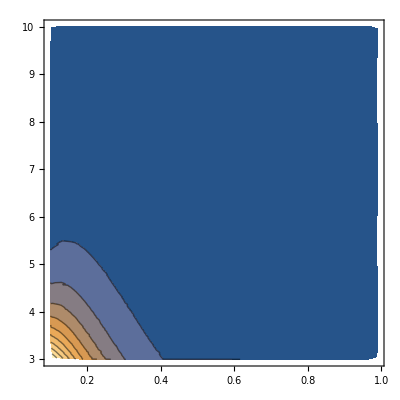

```mathematica
ListContourPlot[data, PlotRange->All]
```

### Ellipsoids

```mathematica
τysmallvEllipsoids={};

For[ellipsoid = sphere,ellipsoid ≤ oblate,ellipsoid++,
τysmallvEllipsoidsIndividual={};
res=resonancesωPlatonicSolids[ϵDrudeAl,polyhedron];
nmax=Length[res];
ωmin=res[[1]]-1;
ωmax=res[[nmax]]+1;
For[vv=0.1,vv≤0.5,vv+=0.1,
AppendTo[τysmallvEllipsoidsIndividual,ParallelTable[{ω,-τ[ω*electronVolt,vv*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPol,ϵDrudeAl, polyhedron]},{ω,ωmin,ωmax,0.00445}]]];
AppendTo[τysmallvEllipsoids,τysmallvEllipsoidsIndividual]];
```

```mathematica
eccentrcty=0.5;
LysmallvEllipsoids={};

For[ellipsoid = sphere,ellipsoid ≤ oblate,ellipsoid++,
AppendTo[LysmallvEllipsoids,ParallelTable[{v,10^3 LIso[v*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPolEllipsoids,ϵDrudeAl, ellipsoid,eccentrcty]},{v,0.1,0.99,0.00445}]]];
```

```mathematica
eccentrcty=0.5;
LysmallbEllipsoids={};

For[ellipsoid = sphere,ellipsoid ≤ oblate,ellipsoid++,
AppendTo[LysmallbEllipsoids,ParallelTable[{b,10^3 LIso[0.5*cSpeedLight,b*nanometer,4/3 π(1*nanometer)^3,αPolEllipsoids,ϵDrudeAl, ellipsoid, eccentrcty]},{b,3,10,0.035}]]];
```

```mathematica
LysmalleEllipsoids={};

For[ellipsoid = sphere,ellipsoid ≤ oblate,ellipsoid++,
AppendTo[LysmalleEllipsoids,ParallelTable[{e,10^5 LIso[0.5*cSpeedLight,3.5*nanometer,4/3 π(1*nanometer)^3,αPolEllipsoids,ϵDrudeAl, ellipsoid, e]},{e,0.1,0.99,0.00445}]]];
```

```mathematica
Export["LysmallvEllipsoids.mx", LysmallvEllipsoids]
Export["LysmallbEllipsoids.mx", LysmallbEllipsoids]
Export["LysmalleEllipsoids.mx", LysmalleEllipsoids]
```

LysmallvEllipsoids.mx

LysmallbEllipsoids.mx

LysmalleEllipsoids.mx

```mathematica
LysmallvEllipsoids=Import["LysmallvEllipsoids.mx"];
LysmallbEllipsoids=Import["LysmallbEllipsoids.mx"];
LysmalleEllipsoids=Import["LysmalleEllipsoids.mx"];
```

```mathematica
oblate
```

3

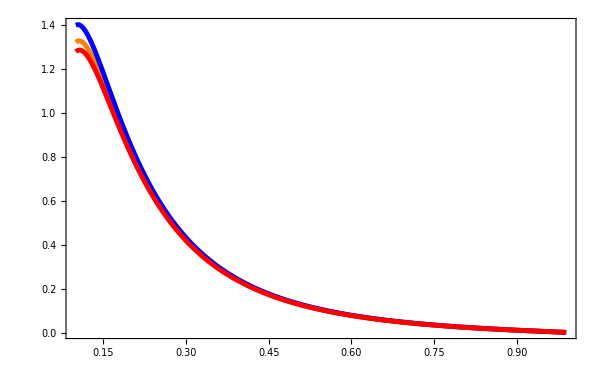

```mathematica
ListLinePlot[
LysmallvEllipsoids,
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["v/c",FontSize->25],MaTeX["\\Delta L \\times 10^{-3} \\,\\hbar ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{prolate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["\\text{b}=3.5\\text{nm}, \\text{e}=0.5",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.62}],
ImageSize->600]
```

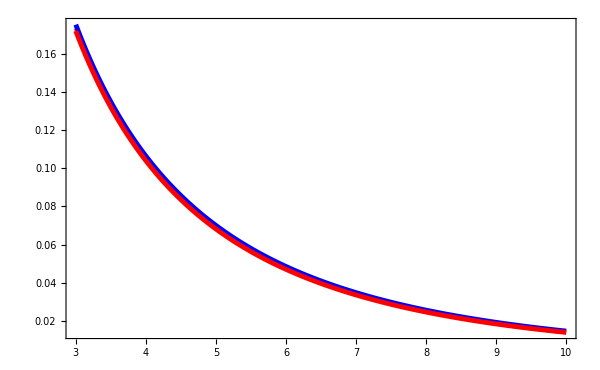

```mathematica
ListLinePlot[
LysmallbEllipsoids,
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["b \\text{[nm]}",FontSize->25],MaTeX["\\Delta L \\times 10^{-3} \\,\\hbar ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{prolate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["v\\text{=0.5}c, e\\text{=0.5}",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.77,0.62}],
ImageSize->600]
```

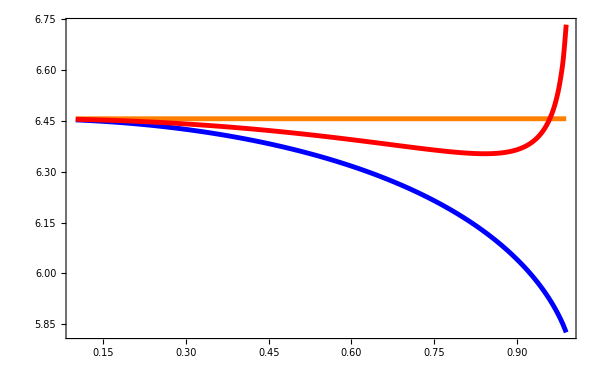

```mathematica
ListLinePlot[
LysmalleEllipsoids,
InterpolationOrder->3,
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["e",FontSize->25],MaTeX["\\Delta L \\times 10^{-5} \\,\\hbar ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{prolate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["b\\text{=3.5nm}, v=\\text{0.5}c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.2,0.62}],
ImageSize->600]
```

```mathematica
[ωFreq_,ϵDielecFunc_,volume_, ellipsoidType_, eccentricity_]
```

```mathematica
αPolEllipsoids[]
Im[ αα[ω,ϵϵ,Vol, ellipsoidType, eccentricity][[1]] + αα[ω,ϵϵ,Vol, ellipsoidType, eccentricity][[3]] ]
```

```mathematica
ωw=1;
NSolve[Im[αPolEllipsoids[ωw,ϵDrudeAl,1, oblate, ee][[1]]+αPolEllipsoids[ωw,ϵDrudeAl,1, oblate, ee][[3]]]==Im[αPolEllipsoids[ωw,ϵDrudeAl,1, sphere, ee][[3]]],ee]
```

NSolve[Im[-(0.0556813-0.000403111 ⅈ)/(3-(0.699712-0.00506565 ⅈ) (1-2 (-(1-ee^2)/(2 ee^2)+(√((1-ee^2)/ee^2) (π/2-ArcTan[√((1-ee^2)/ee^2)]))/(2 ee^2))))-(0.0556813-0.000403111 ⅈ)/(3-(0.699712-0.00506565 ⅈ) (-(1-ee^2)/(2 ee^2)+(√((1-ee^2)/ee^2) (π/2-ArcTan[√((1-ee^2)/ee^2)]))/(2 ee^2)))]==0.00015798,ee]

```mathematica
ωw=1;
ellipsoidd=prolate;
Manipulate[Plot[{Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, ellipsoidd, ee][[1]]+αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, ellipsoidd, ee][[3]]]/(2Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, sphere, ee][[3]]]),Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, oblate, ee][[1]]+αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, oblate, ee][[3]]]/(2Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, sphere, ee][[3]]]),1},{ee,0,1}, PlotRange->All],{ω,0.1,10}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

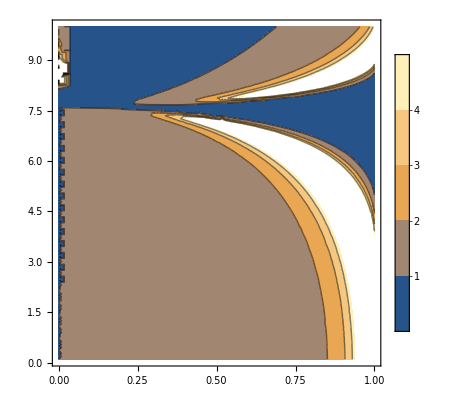

```mathematica
ellipsoidd=prolate;
ContourPlot[Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, ellipsoidd, ee][[1]]+αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, ellipsoidd, ee][[3]]]/(2Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, sphere, ee][[3]]]),{ee,0,1},{ω,0.1,10}, PlotLegends->Automatic]
```

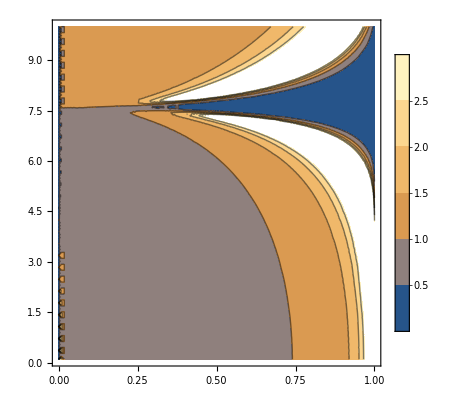

```mathematica
ellipsoidd=oblate;
ContourPlot[Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, ellipsoidd, ee][[1]]+αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, ellipsoidd, ee][[3]]]/(2Im[αPolEllipsoids[ω*electronVolt,ϵDrudeAl,1, sphere, ee][[3]]]),{ee,0,1},{ω,0.1,10}, PlotLegends->Automatic]
```

```mathematica
τ[ω_,v_,b_,Vol_,αα_, ϵϵ_, polyhedronType_]
```

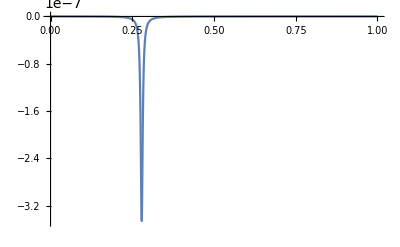

```mathematica
Plot[τ[ω,0.5*cSpeedLight,3.5*nanometer,1,αPol, ϵDrudeAl, sphere],{ω,0,1},PlotRange->All]
```

```mathematica
resonancesωEllipsoids[ϵDrudeAl,oblate,0.5]
```

{7.3612,7.3612,8.01926}

```mathematica
(*Plot[{τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, sphere, 0.5],τ[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPol, ϵDrudeAl, sphere]},{ω,5,10},PlotRange->All]*)
Animate[
Nressphere=Length[resonancesωEllipsoids[ϵDrudeAl,sphere,ee]];
Res1sphere=resonancesωEllipsoids[ϵDrudeAl,sphere,ee][[1]];
lineStylesphere={Thick,Red,Dashed};
maxySpheroids=3;
line1sphere=Line[{{Res1sphere,0},{Res1sphere,1.1*maxySpheroids}}];

Nresprolate=Length[resonancesωEllipsoids[ϵDrudeAl,prolate,ee]];
Res1prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[1]];
Res2prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[ Min[2,Nresprolate] ]];

lineStyleprolate={Thick,Orange,Dashed};
maxySpheroids=3;
line1prolate=Line[{{Res1prolate,0},{Res1prolate,1.1*maxySpheroids}}];
line2prolate=Line[{{Res2prolate,0},{Res2prolate,1.1*maxySpheroids}}];

Nresoblate=Length[resonancesωEllipsoids[ϵDrudeAl,oblate,ee]];
Res1oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[1]];
Res2oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[ Min[3,Nresoblate] ]];

lineStyleoblate={Thick,Blue,Dashed};
maxy=3;
line1oblate=Line[{{Res1oblate,0},{Res1oblate,1.1*maxySpheroids}}];
line2oblate=Line[{{Res2oblate,0},{Res2oblate,1.1*maxySpheroids}}];


Plot[
{-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, prolate, ee] 10^7,-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, oblate, ee] 10^7},{ω,1.5,12.5},
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["\\hbar\\omega \\,\\text{(eV)}",FontSize->25],MaTeX["\\vert\\vert\\vec{\\mathcal{L}}\\vert\\vert \\times 10^{-7} \\,\\text{(a.u.)}",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{prolate}","\\text{oblate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["b\\text{=3.5nm}, v=\\text{0.5}c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.82,0.82}],
ImageSize->600,Epilog->{Directive[lineStyleprolate],line1prolate,line2prolate,Directive[lineStyleoblate],line1oblate,line2oblate, Directive[lineStylesphere],line1sphere}
],{ee,0.1,0.99}]
(*Plot[τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, oblate, 0.5],{ω,5,10},PlotRange->All]*)
```

```mathematica
ccolor={Red, Orange, Blue};
```

3

1.65025

6.28817

3

2.76114

8.15829

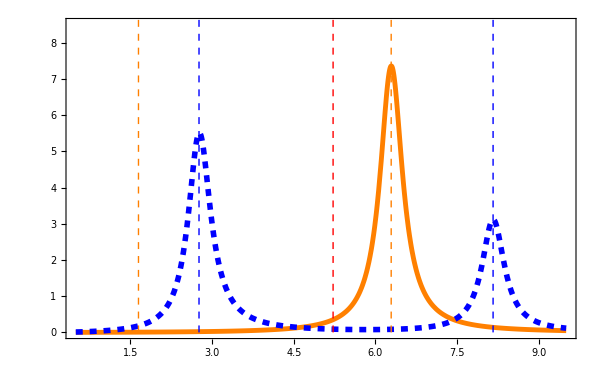

```mathematica
ee=0.99;

Nressphere=Length[resonancesωEllipsoids[ϵDrudeAl,sphere,ee]];
Res1sphere=resonancesωEllipsoids[ϵDrudeAl,sphere,ee][[1]];
lineStylesphere={Thick,Red,Dashed};
maxySpheroids=9;
line1sphere=Line[{{Res1sphere,0},{Res1sphere,1.1*maxySpheroids}}];

Nresprolate=Length[resonancesωEllipsoids[ϵDrudeAl,prolate,ee]]
Res1prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[1]]
Res2prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[ Min[2,Nresprolate] ]]

lineStyleprolate={Thick,Orange,Dashed};
maxySpheroids=9;
line1prolate=Line[{{Res1prolate,0},{Res1prolate,1.1*maxySpheroids}}];
line2prolate=Line[{{Res2prolate,0},{Res2prolate,1.1*maxySpheroids}}];

Nresoblate=Length[resonancesωEllipsoids[ϵDrudeAl,oblate,ee]]
Res1oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[1]]
Res2oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[ Min[3,Nresoblate] ]]

lineStyleoblate={Thick,Blue,Dashed};
maxy=3;
line1oblate=Line[{{Res1oblate,0},{Res1oblate,1.1*maxySpheroids}}];
line2oblate=Line[{{Res2oblate,0},{Res2oblate,1.1*maxySpheroids}}];

Plot[
{-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, prolate, ee] 10^8,-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, oblate, ee] 10^8},{ω,0.5,9.5},
PlotRange->{All,{0,8.5}},
Frame->True,
FrameLabel->{MaTeX["\\hbar\\omega \\,\\text{(eV)}",FontSize->25],MaTeX["\\vert\\vert\\vec{\\mathcal{L}}\\vert\\vert \\times 10^{-8} \\,\\text{(a.u.)}",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[4.0], Dashed},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{prolate}","\\text{oblate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
(*LegendLabel->MaTeX["b\\text{=3.5nm}, v=\\text{0.5}c",FontSize->20],*)
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.40,0.82}],
ImageSize->600,Epilog->{Directive[lineStyleprolate],line1prolate,line2prolate,Directive[lineStyleoblate],line1oblate,line2oblate, Directive[lineStylesphere],line1sphere}
]
```

```mathematica
lineStylesphere
```

{Thickness[Large],RGBColor[0, 1, 0],Dashing[{Small,Small}]}

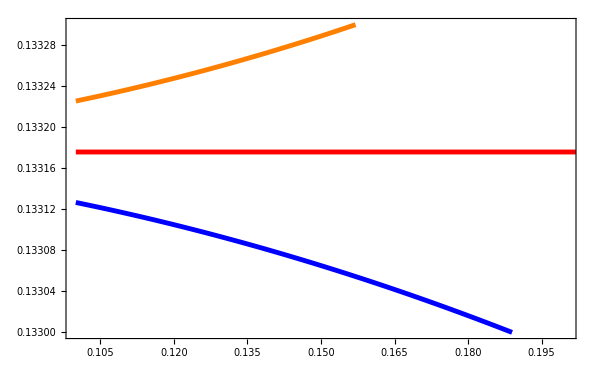

```mathematica
ListLinePlot[
LysmalleEllipsoids,
InterpolationOrder->3,
PlotRange->{{0.1,0.2},{0.133,0.1333}},
Frame->True,
FrameLabel->{MaTeX["e",FontSize->25],MaTeX["\\Delta L \\times 10^{-3} \\,\\hbar ",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{ccolor[[1]],AbsoluteThickness[3.5]},{ccolor[[2]],AbsoluteThickness[3.5]},{ccolor[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
(*PlotLegends->Placed[LineLegend[MaTeX[{"\\text{sphere}","\\text{prolate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["b\\text{=3.5nm}, v=\\text{0.5}c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.19,0.78}],*)
ImageSize->600]
```

```mathematica
}
```

```mathematica
Nresprolate=Length[resonancesωEllipsoids[ϵDrudeAl,prolate,ee]]
Res1prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[1]]
Res2prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[ Min[2,Nresprolate] ]]

Nresoblate=Length[resonancesωEllipsoids[ϵDrudeAl,oblate,ee]]
Res1oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[1]]
Res2oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[ Min[3,Nresoblate] ]]
```

3

7.58675

7.58697

3

7.58682

7.58705

0.8

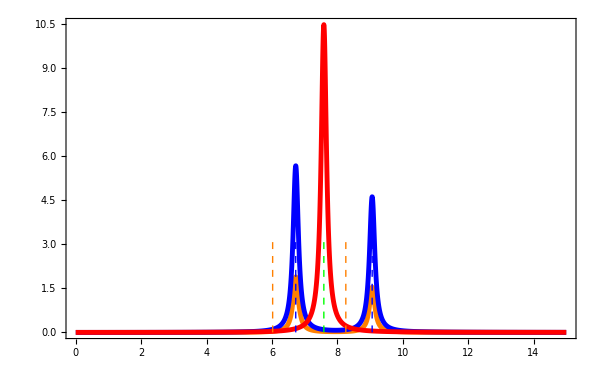

```mathematica
Nressphere=Length[resonancesωEllipsoids[ϵDrudeAl,sphere,ee]];
Res1sphere=resonancesωEllipsoids[ϵDrudeAl,sphere,ee][[1]];
lineStylesphere={Thick,Red,Dashed};
maxySpheroids=3;
line1sphere=Line[{{Res1sphere,0},{Res1sphere,1.1*maxySpheroids}}];

Nresprolate=Length[resonancesωEllipsoids[ϵDrudeAl,prolate,ee]];
Res1prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[1]];
Res2prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[ Min[2,Nresprolate] ]];

lineStyleprolate={Thick,Orange,Dashed};
maxySpheroids=3;
line1prolate=Line[{{Res1prolate,0},{Res1prolate,1.1*maxySpheroids}}];
line2prolate=Line[{{Res2prolate,0},{Res2prolate,1.1*maxySpheroids}}];

Nresoblate=Length[resonancesωEllipsoids[ϵDrudeAl,oblate,ee]];
Res1oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[1]];
Res2oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[ Min[3,Nresoblate] ]];

lineStyleoblate={Thick,Blue,Dashed};
maxy=3;
line1oblate=Line[{{Res1oblate,0},{Res1oblate,1.1*maxySpheroids}}];
line2oblate=Line[{{Res2oblate,0},{Res2oblate,1.1*maxySpheroids}}];


ee=0.8
Nressphere=Length[resonancesωEllipsoids[ϵDrudeAl,sphere,ee]];
Res1sphere=resonancesωEllipsoids[ϵDrudeAl,sphere,ee][[1]];
lineStylesphere={Thick,Green,Dashed};
maxySpheroids=3;
line1sphere=Line[{{Res1sphere,0},{Res1sphere,1.1*maxySpheroids}}];

Nresprolate=Length[resonancesωEllipsoids[ϵDrudeAl,prolate,ee]];
Res1prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[1]];
Res2prolate=resonancesωEllipsoids[ϵDrudeAl,prolate,ee][[ Min[2,Nresprolate] ]];

lineStyleprolate={Thick,Orange,Dashed};
maxySpheroids=3;
line1prolate=Line[{{Res1prolate,0},{Res1prolate,1.1*maxySpheroids}}];
line2prolate=Line[{{Res2prolate,0},{Res2prolate,1.1*maxySpheroids}}];

Nresoblate=Length[resonancesωEllipsoids[ϵDrudeAl,oblate,ee]];
Res1oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[1]];
Res2oblate=resonancesωEllipsoids[ϵDrudeAl,oblate,ee][[ Min[3,Nresoblate] ]];

lineStyleoblate={Thick,Blue,Dashed};
maxy=3;
line1oblate=Line[{{Res1oblate,0},{Res1oblate,1.1*maxySpheroids}}];
line2oblate=Line[{{Res2oblate,0},{Res2oblate,1.1*maxySpheroids}}];
Plot[
{-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, oblate, ee] 10^7,-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,3,αPolEllipsoids, ϵDrudeAl, oblate, ee] 10^7,
-τIso[ω*electronVolt,0.5*cSpeedLight,3.5*nanometer,3,αPolEllipsoids, ϵDrudeAl, sphere, ee] 10^7},{ω,0,15},
PlotRange->{All,All},
Frame->True,
FrameLabel->{MaTeX["\\hbar\\omega \\,\\text{(eV)}",FontSize->25],MaTeX["\\vert\\vert\\vec{\\mathcal{L}}\\vert\\vert \\times 10^{-7} \\,\\text{(a.u.)}",FontSize->25]},
FrameStyle->Thick,
FrameTicksStyle->Directive[AbsoluteThickness[2], Black,FontFamily->"LMRoman17", 20],
(*GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thick,Opacity[0.5]],*)
PlotStyle->{{color[[1]],AbsoluteThickness[3.5]},{color[[2]],AbsoluteThickness[3.5]},{color[[3]],AbsoluteThickness[3.5]},{color[[4]],AbsoluteThickness[3.5]},{color[[5]],AbsoluteThickness[3.5]},{color[[6]],AbsoluteThickness[3.5]}},
PlotLegends->Placed[LineLegend[MaTeX[{"\\text{prolate}","\\text{oblate}","\\text{oblate}","\\text{octahedron}","\\text{hexahedron}","\\text{tetrahedron}"},FontSize->20],
LegendLabel->MaTeX["b\\text{=3.5nm}, v=\\text{0.5}c",FontSize->20],
LegendFunction->(Framed[#,RoundingRadius->6,Background->White,FrameStyle->{Black,Thick},FrameMargins->1]&),
LegendMargins->1,LabelStyle->Directive[Black,FontFamily->"Cambria", 20],Spacings->0.01],{0.82,0.82}],
ImageSize->600,Epilog->{Directive[lineStyleprolate],line1prolate,line2prolate,Directive[lineStyleoblate],line1oblate,line2oblate, Directive[lineStylesphere],line1sphere}
]
```

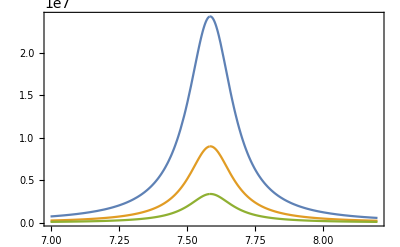

```mathematica
Plot[{-τIso[ω*electronVolt,0.2*cSpeedLight,5.5*nanometer,4/3 π (5*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.4*cSpeedLight,5.5*nanometer,4/3 π (5*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.6*cSpeedLight,5.5*nanometer,4/3 π (5*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7},{ω,7,8.2}, PlotRange->All, Frame->True]
```

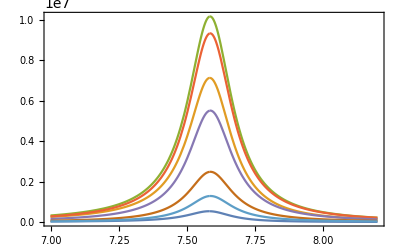

```mathematica
Plot[{
-τIso[ω*electronVolt,0.1*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.2*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.3*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.4*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.6*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.8*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,
-τIso[ω*electronVolt,0.9*cSpeedLight,12*nanometer,4/3 π (10*nanometer)^3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7},{ω,7,8.2}, PlotRange->All, Frame->True]
```

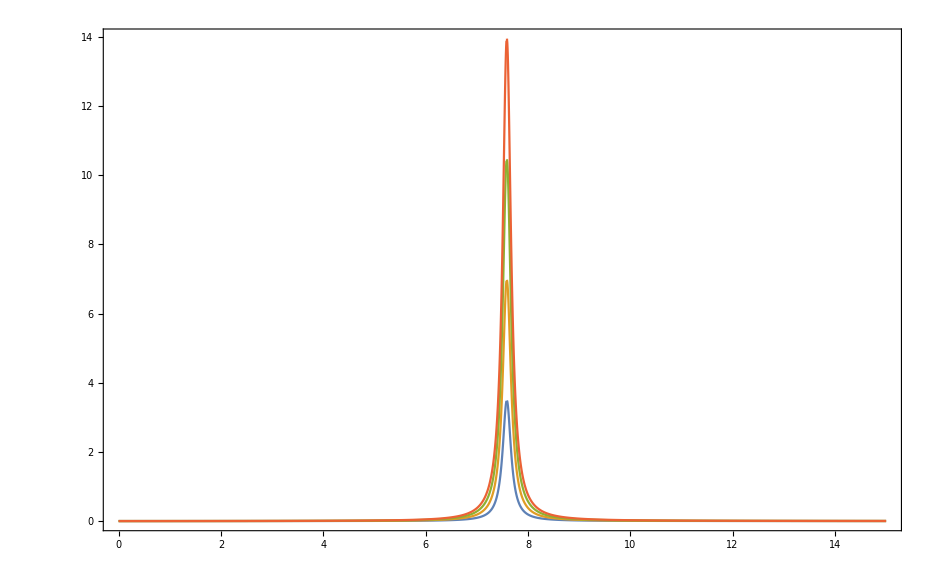

```mathematica
Plot[{-τIso[ω*electronVolt,0.5*cSpeedLight,5.5*nanometer,1,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,-τIso[ω*electronVolt,0.5*cSpeedLight,5.5*nanometer,2,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,-τIso[ω*electronVolt,0.5*cSpeedLight,5.5*nanometer,3,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7,-τIso[ω*electronVolt,0.5*cSpeedLight,5.5*nanometer,4,αPolEllipsoids, ϵDrudeAl, sphere, 1] 10^7},{ω,0,15}, PlotRange->All, Frame->True]
```

```mathematica
a=2;
b[e_]=a √(1-e^2);
c[e_]=b[e];
ee=0.5;
Manipulate[ParametricPlot3D[{a*Cos[u]*Sin[v],b[ee]*Sin[u]*Sin[v],c[ee]*Cos[v]},{u,0,2π},{v,0,π}],{ee,0,1}]
```

```mathematica
a=2;
b2[e_]=a;
c2[e_]=a √(1-e^2);
ee=0.5
Manipulate[ParametricPlot3D[{a*Cos[u]*Sin[v],b2[ee]*Sin[u]*Sin[v],c2[ee]*Cos[v]},{u,0,2π},{v,0,π}],{ee,0,1}]
```

0.5

### Mie

```mathematica
k[ω_]:=ω/cSpeedLight
ωl[l_]:=ω*√(l/(2*l+1))


(*         Acá meto lo de la α(ω) completa         *)

j[n_,z_]:= SphericalBesselJ[n,z]
h[n_,z_]:=SphericalHankelH1[n,z]

dj[n_,z_]:=-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z])
dh[n_,z_]:=-SphericalHankelH1[n,z]/(2 z)+1/2 (SphericalHankelH1[-1+n,z]-SphericalHankelH1[1+n,z])

H[n_,z_]:=z h[n,z]
J[n_,z_]:=z j[n,z]
dH[n_,z_]:=SphericalHankelH1[n,z]+z (-SphericalHankelH1[n,z]/(2 z)+1/2 (SphericalHankelH1[-1+n,z]-SphericalHankelH1[1+n,z]))
dJ[n_,z_]:=SphericalBesselJ[n,z]+z (-SphericalBesselJ[n,z]/(2 z)+1/2 (SphericalBesselJ[-1+n,z]-SphericalBesselJ[1+n,z]))

x0[ω_,a_]:=ω a/cSpeedLight
xi[ω_,a_]:=ω a Sqrt[ϵDrudeAl[ω]]/ cSpeedLight
xiϵ[ϵ_,a_]:=ω a Sqrt[ϵ]/ cSpeedLight

tE[l_,ω_,a_]:=-I(((1/ Sqrt[ϵDrudeAl[ω]])j[l,x0[ω,a]]dJ[l,xi[ω,a]] -  Sqrt[ϵDrudeAl[ω]]j[l,xi[ω,a]]dJ[l,x0[ω,a]])/(Sqrt[ϵDrudeAl[ω]]j[l,xi[ω,a]]dH[l,x0[ω,a]] - (1/Sqrt[ϵDrudeAl[ω]])h[l,x0[ω,a]]dJ[l,xi[ω,a]] ))

tEϵ[l_,ϵ_,ω_,a_]:=-I(((1/ Sqrt[ϵ])j[l,x0[ω,a]]dJ[l,xi[ω,a]] -  Sqrt[ϵ]j[l,xi[ω,a]]dJ[l,x0[ω,a]])/(Sqrt[ϵ]j[l,xi[ω,a]]dH[l,x0[ω,a]] - (1/Sqrt[ϵ])h[l,x0[ω,a]]dJ[l,xi[ω,a]] ))

αMie[ω_,a_]:=(3*tE[1,ω,a])/(2*(k[ω])^3)
```

```mathematica
ϵλ[ω_,V_]=1-(1+2(2π tE[1,ω,((3V)/(4π))^(1/3)])/(V*k[ω]^3))/((2π tE[1,ω,((3V)/(4π))^(1/3)])/(V*k[ω]^3));
```

```mathematica
ϵλ[0.27881318539392536,1]
```

-1.00017+0.0259615 ⅈ

```mathematica
αPolMie[ωFreq_,ϵDielecFunc_,volume_, polyhedronType_]:=Module[
{ω=ωFreq,ϵ=ϵDielecFunc,V=volume, polyhedron=polyhedronType},
Switch[polyhedron,(*Compare the variable polyhedron to one of the possible platonic solids*)
sphere,3((ϵ[ω]+2)/(2*k[ω]^3))tE[1,ω,((3V)/(4π))^(1/3)] 1/(ϵ[ω]+2),
icosahedron,(3.1304)*((ϵ[ω]+2)/(2*k[ω]^3))tE[1,ω,((3V)/(4π))^(1/3)]*(ϵ[ω]^2+3.04968ϵ[ω]+4.0896*1.5236/3.1304)/(ϵ[ω]^3+5.29169 ϵ[ω]^2+8.52687ϵ[ω]+4.0896),
dodecahedron, (3.1779)*((ϵ[ω]+2)/(2*k[ω]^3))tE[1,ω,((3V)/(4π))^(1/3)]*(ϵ[ω]^2+2.42101ϵ[ω]+2.56842*1.5422/3.1779)/(ϵ[ω]^3+4.72932 ϵ[ω]^2+6.53464ϵ[ω]+2.56842),
octahedron,(3.5507)*((ϵ[ω]+2)/(2*k[ω]^3))tE[1,ω,((3V)/(4π))^(1/3)]*(ϵ[ω]^3+5.13936 ϵ[ω]^2+5.86506ϵ[ω]+1.5871)/(ϵ[ω]^4+8.26227 ϵ[ω]^3+19.8267 ϵ[ω]^2+15.6191ϵ[ω]+3.5507),
hexahedron,(3.6442)*((ϵ[ω]+2)/(2*k[ω]^3))tE[1,ω,((3V)/(4π))^(1/3)]*(ϵ[ω]^3+4.83981 ϵ[ω]^2+5.54742ϵ[ω]+1.6383)/(ϵ[ω]^4+8.0341 ϵ[ω]^3+19.3534 ϵ[ω]^2+15.4349ϵ[ω]+3.6442),
tetrahedron,(5.0285)*((ϵ[ω]+2)/(2*k[ω]^3))tE[1,ω,((3V)/(4π))^(1/3)]*(ϵ[ω]^3+7.65667 ϵ[ω]^2+8.50919ϵ[ω]+1.8063)/(ϵ[ω]^4+14.1983 ϵ[ω]^3+44.9182 ϵ[ω]^2+30.2668ϵ[ω]+5.0285)
]
]
```

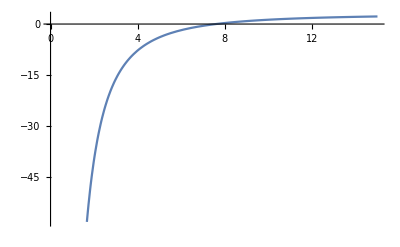

```mathematica
Plot[Re[ϵDrudeAl[ω*electronVolt]+2],{ω,0,15}]
```

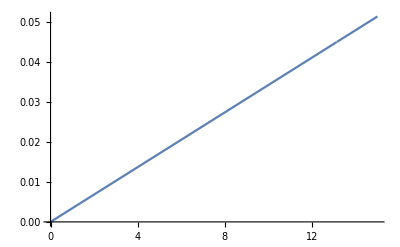

```mathematica
Plot[Im[ϵλ[ω*electronVolt,1*nanometer]+2],{ω,0,15}]
```

```mathematica
NSolve[ϵλ[ω,1]+2==0,ω]
```

$Aborted

```mathematica
soldrude=NSolve[ϵDrudeAl[ω]+2==0,ω]
```

{{ω→-0.278813-0.00361981 ⅈ},{ω→0.278813-0.00361981 ⅈ}}

```mathematica
ϵDrudeAl[ω]/.soldrude//Chop
ϵλ[ω,1]/.soldrude//Chop
```

{-2.,-2.}

{-0.999999+3.17522×10^-8 ⅈ,-0.999999-3.17522×10^-8 ⅈ}

```mathematica
vv=4/3 π*(1*nanometer)^3
NSolve[ϵλ[ω,1]+2==0,ω]
```

28267.4

```mathematica
$Aborted
```

```mathematica
{{ω->-0.35207106285660494-0.003619806050000018 ⅈ},{ω->-0.2921378940439779-0.003619806049999981 ⅈ},{ω->-0.2518184740497445-0.0036198060499999947 ⅈ},{ω->0.25181847404974417-0.0036198060500000043 ⅈ},{ω->0.29213789404397794-0.003619806050000002 ⅈ},{ω->0.35207106285660467-0.003619806049999998 ⅈ}}*
```

```mathematica
resonancesωPlatonicSolids[ϵDrudeAl,icosahedron]
```

{6.85233,7.94948,9.58035}

### Rotation

```mathematica
resonancesωEllipsoids[ϵDrudeAl,prolate,0.5]
αPolTheta[10*electronVolt, ϵDrudeAl, 1, 0.0*Degree,0.5]//MatrixForm
```

{7.14737,7.79738,7.79738}

(-0.280577+0.0113022 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.349807+0.0175835 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.349807+0.0175835 ⅈ)

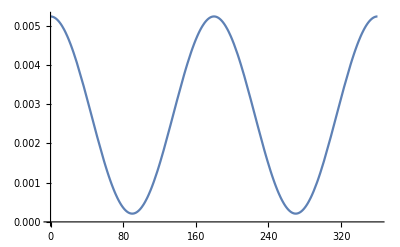

```mathematica
ω1=resonancesωEllipsoids[ϵDrudeAl,prolate,0.5][[1]];
vvel=0.5;
bImpctPrm=3.5;
eccntrcty=0.5;
Plot[-τy[ω1*electronVolt,vvel*cSpeedLight,bImpctPrm*nanometer,4/3 π(1*nanometer)^3,αPolTheta,ϵDrudeAl, angleTheta*Degree,eccntrcty],{angleTheta,0,360}]
```

## Figures

```mathematica
labels
```

{Sphere,Icosahedron,Dodecahedron,Octahedron,Hexahedron,Tetrahedron}

```mathematica
Graphics3D[Octahedron[]]
```

-Graphics3D-